```mathematica
Derivative[0,1,0,0][Hypergeometric2F1][5,0,2,x]-Derivative[1,0,0,0][Hypergeometric2F1][3,0,2,x]//FunctionExpand
```

Hypergeometric2F1^(0,1,0,0)[3,0,2,x]-Hypergeometric2F1^(1,0,0,0)[3,0,2,x]

```mathematica
Θ[1,1,n,θ]//FunctionExpand
```

(√3 Ri si Hypergeometric2F1[1-n/2,(4+n)/2,2,Ri^2/B^2])/(2 B^2)

```mathematica
Θ[3,1,-4,θ]
```

(8 B^2 Ri (3-(3 Ri^2)/B^2+Ri^4/B^4))/(9 √3 si^3)

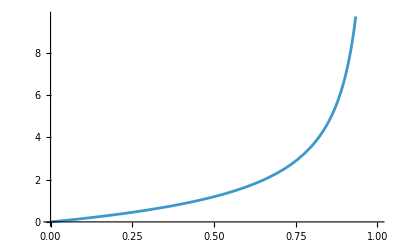

```mathematica
Plot[Derivative[0,1,0,0][Hypergeometric2F1][3,0,2,x]-Derivative[1,0,0,0][Hypergeometric2F1][3,0,2,x],{x,0,1}]
```

```mathematica
EnhancedHypergeomSimplify@SeriesCoefficient[B^n1 Θ[3,3,n1,θ]Exp[ I 3 θRi]Exp[- I 3 θsi],{n1,-4,0}]
```

1/(16 B^4)ⅇ^(3 ⅈ (θRi-θsi)) Sin[2 ArcTan[(2 Ri)/(√3 si)]]^3 (-(6 B^10)/(Ri^2 (B^2-Ri^2)^4)+4 (-1+B^4/Ri^4) (Hypergeometric2F1^(0,1,0,0)[5,2,1,Ri^2/B^2]-Hypergeometric2F1^(1,0,0,0)[5,2,1,Ri^2/B^2])-(4 (B^4+5 B^2 Ri^2+4 Ri^4) (Hypergeometric2F1^(0,1,0,0)[5,2,2,Ri^2/B^2]-Hypergeometric2F1^(1,0,0,0)[5,2,2,Ri^2/B^2]))/Ri^4)

```mathematica
EnhancedHypergeomSimplify[Derivative[0,1,0,0][Hypergeometric2F1][5,2,1,Ri^2/B^2]-Derivative[1,0,0,0][Hypergeometric2F1][5,2,1,Ri^2/B^2]]
```

Hypergeometric2F1^(0,1,0,0)[5,2,1,Ri^2/B^2]-Hypergeometric2F1^(1,0,0,0)[5,2,1,Ri^2/B^2]

```mathematica
B^-4 Θ[3,3,-4,θ]Exp[ I 3 θRi]Exp[- I 3 θsi]
```

(2 ⅇ^(3 ⅈ θRi-3 ⅈ θsi) Ri^3 (3+Cos[2 ArcTan[(2 Ri)/(√3 si)]]))/(3 √3 B^4 si^3)

```mathematica
B^-4 Θ[3,3,-4,θ]
```

(2 Ri^3 (3+Cos[2 ArcTan[(2 Ri)/(√3 si)]]))/(3 √3 B^4 si^3)

```mathematica
psi111[-4,3,-1,3,1,B,θ,θsi,ϕsi,θRi,ϕRi,0]
```

1/(16 B^4)ⅇ^(3 ⅈ (θRi-θsi)) Sin[2 ArcTan[(2 Ri)/(√3 si)]]^3 (-(6 B^10)/(Ri^2 (B^2-Ri^2)^4)+4 (-1+B^4/Ri^4) (Hypergeometric2F1^(0,1,0,0)[5,2,1,Ri^2/B^2]-Hypergeometric2F1^(1,0,0,0)[5,2,1,Ri^2/B^2])-(4 (B^4+5 B^2 Ri^2+4 Ri^4) (Hypergeometric2F1^(0,1,0,0)[5,2,2,Ri^2/B^2]-Hypergeometric2F1^(1,0,0,0)[5,2,2,Ri^2/B^2]))/Ri^4)

```mathematica
Θ[1,1,n,θ]
```

(√3 Ri si Hypergeometric2F1[1-n/2,(4+n)/2,2,Ri^2/B^2])/(2 B^2)

```mathematica
Hypergeometric2F1[1-n/2,(4+n)/2,5/2,Ri^2/B^2]//FunctionExpand
```

-(3 B^2 Cos[n ArcSin[Ri/B]])/((1+n) (2+n) Ri^2)+(3 B^3 (1+(n Ri^2)/B^2) Sin[n ArcSin[Ri/B]])/(n (1+n) (2+n) Ri^3 √(1-Ri^2/B^2))

```mathematica
Derivative[0,1,0,0][Hypergeometric2F1][3,0,2,Ri^2/B^2]-Derivative[1,0,0,0][Hypergeometric2F1][3,0,2,Ri^2/B^2]//FunctionExpand
```

Hypergeometric2F1^(0,1,0,0)[3,0,2,Ri^2/B^2]-Hypergeometric2F1^(1,0,0,0)[3,0,2,Ri^2/B^2]

```mathematica
Derivative[0,1,0,0][Hypergeometric2F1][3,0,2,Ri^2/B^2]-Derivative[1,0,0,0][Hypergeometric2F1][3,0,2,Ri^2/B^2]
```

```mathematica
psi111[n_,ls_,ms_,lR_,mR_,B_,θ_,θsi_,ϕsi_,θRi_,ϕRi_,log_:0]
```

```mathematica
ⅈ/(√3)(psi111[2,1,1,1,-1,B,θ,θsi,ϕsi,θRi,ϕRi]-psi111[2,1,-1,1,1,B,θ,θsi,ϕsi,θRi,ϕRi])//FullSimplify//TrigExpand//FullSimplify//FunctionExpand
```

Ri si Sin[θRi-θsi]

```mathematica
ⅈ/(√3)(psi111[2,1,1,1,-1,B,θ,θsi,ϕsi,θRi,ϕRi]-psi111[2,1,-1,1,1,B,θ,θsi,ϕsi,θRi,ϕRi])//FullSimplify//TrigExpand//FullSimplify//FunctionExpand
```

Ri si Sin[θRi-θsi]

```mathematica
(Derivative[0,1,0,0][Hypergeometric2F1][1,2,2,(3 si^2)/(4 B^2)]-Derivative[1,0,0,0][Hypergeometric2F1][1,2,2,(3 si^2)/(4 B^2)])/(2 B^2)
```

```mathematica
Series[B^(-2+n) Ri si Hypergeometric2F1[1-n/2,(4+n)/2,2,(3 si^2)/(4 B^2)] Sin[θRi-θsi],{n,0,3}]
```

```mathematica
Derivative[db,da,dc,dz][Hypergeometric2F1][a_,0,c_,z_]
```

Hypergeometric2F1^(db,da,dc,dz)[a_,0,c_,z_]

```mathematica
Derivative[0,1,0,0][Hypergeometric2F1][0,3,2,x]/.{x->2}//N
```

0

```mathematica
finalResult/.z->Ri^2/B^2
```

Ri^2/(2 B^2 (-1+Ri^2/B^2))+Log[1-Ri^2/B^2]

```mathematica
-(x/(2 (-1+x))+Log[1-x])-(Derivative[0,1,0,0][Hypergeometric2F1][3,0,2,x]-Derivative[1,0,0,0][Hypergeometric2F1][3,0,2,x]
)/.{x->0.3}//N
```

1.11022×10^-16

```mathematica
(*雅可比坐标,不用B,θ表示*)
BθToRs={B->√(Ri^2+3/4 si^2),θ-> ArcTan[(2 Ri)/(√3 si)]};
StandardAssumption={B>0,θsi>0,θsi<π,θRi>0,θRi<π,ϕsi>0,ϕsi<2π,ϕRi>0,ϕRi<2π,si>0,Ri>0,t>0}
sii={si Cos[θsi],si Sin[θsi]};
Rii={Ri Cos[θRi],Ri Sin[θRi]};
s1=-1/2 sii+Rii;
R1=-3/4 sii-1/2 Rii;
s3=-1/2 sii-Rii;
R3=3/4 sii-1/2 Rii;
θs1=Simplify[ArcTan[s1[[1]],s1[[2]]],Assumptions->StandardAssumption];
θR1=Simplify[ArcTan[R1[[1]],R1[[2]]],Assumptions->StandardAssumption];
θs3=Simplify[ArcTan[s3[[1]],s3[[2]]],Assumptions->StandardAssumption];
θR3=Simplify[ArcTan[R3[[1]],R3[[2]]],Assumptions->StandardAssumption];
s1B=√(s1[[1]]^2+s1[[2]]^2)//FullSimplify;
s3B=√(s3[[1]]^2+s3[[2]]^2)//FullSimplify;
R1B=√(R1[[1]]^2+R1[[2]]^2)//FullSimplify;
R3B=√(R3[[1]]^2+R3[[2]]^2)//FullSimplify;
(*要展开到的阶数*)
nMax=0;
Ltot=0;
M=0;
(*超球谐函数的通式*)
Θ1[ls_,lR_,n_,θ_]:=Θ1[ls,lR,n,θ]=FullSimplify[
((Cos[θ])^-ls ReducedHypergeometric[1/2 (lR-ls-n),1/2 (2+lR-ls+n),1+lR,Sin[θ]^2] ( Sin[θ])^lR)//FunctionExpand//FullSimplify,Assumptions->{θ>0,θ<π/2}]/.{Cos[θ]->(√3 si)/(2 B),Sin[θ]->Ri/B,Csc[θ]->(Ri/B)^-1,Sec[θ]->((√3 si)/(2 B))^-1}/.θ-> ArcTan[(2 Ri)/(√3 si)];
Θ[ls_,lR_,n_,θ_]:=Θ[ls,lR,n,θ]=FullSimplify[
(ReducedHypergeometric[1/2(lR+ls-n),1/2(2+lR+ls+n),lR+1,Sin[θ]^2] Sin[θ]^lR Cos[θ]^ls)//FunctionExpand//FullSimplify,Assumptions->{θ>0,θ<π/2}]/.{Cos[θ]->(√3 si)/(2 B),Sin[θ]->Ri/B,Csc[θ]->(Ri/B)^-1,Sec[θ]->((√3 si)/(2 B))^-1}/.θ-> ArcTan[(2 Ri)/(√3 si)];
(*超几何函数化简*)
HypergeomSimplify[expr_]:=Module[{result},result=(expr//FunctionExpand)//.{(*b=0 时对 a 的导数为 0*)d_.*Derivative[da_,db_,dc_,dz_][Hypergeometric2F1][a_,0,c_,z_]/;da>0&&db==0&&dc==0&&dz==0:>0,(*a=0 时对 a 的导数为 0*)d_.*Derivative[da_,db_,dc_,dz_][Hypergeometric2F1][0,b_,c_,z_]/;da==0&&db>0&&dc==0&&dz==0:>0,(*一般导数情况-对 a 的导数*)
d_.*Derivative[da_,db_,dc_,dz_][Hypergeometric2F1][a_,b_,a_,z_]/;da==0&&db>=0&&dc==0&&dz==0:>d*(-1)^db (1-z)^-b Log[1-z]^db,
d_.*Derivative[da_,db_,dc_,dz_][Hypergeometric2F1][a_,b_,b_,z_]/;da>=0&&db==0&&dc==0&&dz==0:>d*(-1)^da (1-z)^-a Log[1-z]^da,
d_.*Derivative[da_,db_,dc_,dz_][Hypergeometric2F1][a_,b_,c_,z_]/;da>0&&db==0&&dc==0&&dz==0:>d*Sum[(Limit[D[Pochhammer[α,k],{α,da}], α->a])*(Pochhammer[b,k]/(Pochhammer[c,k] k!))*z^k,{k,0,Infinity}],(*对 b 的导数*)
d_.*Derivative[da_,db_,dc_,dz_][Hypergeometric2F1][a_,b_,c_,z_]/;da==0&&db>0&&dc==0&&dz==0:>d*Sum[(Limit[D[Pochhammer[β,k],{β,db}], β->b])*(Pochhammer[a,k]/(Pochhammer[c,k] k!))*z^k,{k,0,Infinity}],(*对 c 的导数*)d_.*Derivative[da_,db_,dc_,dz_][Hypergeometric2F1][a_,b_,c_,z_]/;da==0&&db==0&&dc>0&&dz==0:>d*Sum[(D[1/Pochhammer[γ,k],{γ,dc}]/. γ->c)*((Pochhammer[a,k] Pochhammer[b,k])/k!*z^k),{k,0,Infinity}],
d_.*Derivative[da_,db_,dc_,dz_][Hypergeometric2F1][a_,b_,c_,z_]/;(dc==0&&dz==0):>d*Sum[If[da==0&&db==0,(*零阶导数情况*)Pochhammer[a,k]*Pochhammer[b,k]/(Pochhammer[c,k]*k!),(*高阶导数情况*)Module[{α,β},Limit[Limit[D[D[Pochhammer[α,k]*Pochhammer[β,k]/(Pochhammer[c,k]*k!),{α,da}],{β,db}],β->b],α->a]]]*z^k,{k,0,Infinity}]
};
(*尝试完全化简*)
result 
];
(*111展开*)
psi111[n_,ls_,ms_,lR_,mR_,B_,θ_,θsi_,ϕsi_,θRi_,ϕRi_,log_:0]:=B^n Θ[ls,lR,n,θ]Exp[mR I lR θRi]Exp[ms I ls θsi]/;log==0
psi111[n_,ls_,ms_,lR_,mR_,B_,θ_,θsi_,ϕsi_,θRi_,ϕRi_,log_:0]:=SeriesCoefficient[B^n1 Θ[ls,lR,n1,θ]Exp[mR I lR θRi]Exp[ms I ls θsi],{n1,n,log}]/;log!=0
psi1111[n_,ls_,ms_,lR_,mR_,B_,θ_,θsi_,ϕsi_,θRi_,ϕRi_,log_:0]:=SeriesCoefficient[B^n1 Θ[ls,lR,n1,θ]Exp[mR I lR θRi]Exp[ms I ls θsi],{n1,n,log}]

(*两体特殊函数定义*)
TwoBodyF[s_,p_,l_,m_]:=Log[s/Subscript[a, l]]Y[l,m,θsi,ϕsi]/;p==0&&l==0
TwoBodyF[s_,p_,l_,m_]:=(s^l/(2l)!!-(2(2l-2)!! Subscript[a, l])/(π s^l))Y[l,m,θsi,ϕsi]/;p==0&&l>=1
TwoBodyF[s_,p_,l_,m_]:=(-1/4 s^2 Log[s/Subscript[a, l]]+s^2/4-(π Subscript[r, l])/4)Y[l,m,θsi,ϕsi]/;p==1&&l==0
TwoBodyF[s_,p_,l_,m_]:=(-s^3/16+(Subscript[a, l] s)/π Log[s/Subscript[Rc, l]])Y[l,m,θsi,ϕsi]/;p==1&&l==1
TwoBodyF[s_,p_,l_,m_]:=((-(s^(l+2)/(2(2l+2)!!))-((2l-4)!! Subscript[a, l])/(π s^(l-2))-(Subscript[a, l] Subscript[r, l] s^l)/(2(2l)!!))Y[l,m,θsi,ϕsi])/;p==1&&l>=2
(*领头阶*)
(*B0[n_,ls_,lR_,ms_,mR_,si_,Ri_,θsi_,ϕsi_,θRi_,ϕRi_]:=psi111[0,0,0,0,0,B,θ,θsi,ϕsi,θRi,ϕRi,3]//FullSimplify//TrigExpand*)
B0[n_,ls_,lR_,ms_,mR_,si_,Ri_,θsi_,ϕsi_,θRi_,ϕRi_]:=ⅈ/(√3)(psi111[2,1,1,1,-1,B,θ,θsi,ϕsi,θRi,ϕRi]-psi111[2,1,-1,1,1,B,θ,θsi,ϕsi,θRi,ϕRi])//FullSimplify//TrigExpand
(*B0[n_,ls_,lR_,ms_,mR_,si_,Ri_,θsi_,ϕsi_,θRi_,ϕRi_]:=32/3 √(2/15) π psi111[2,2,2,0,0,B,θ,θsi,ϕsi,θRi,ϕRi]*)
(*展开111式*)
Psi111sum[Psi111_]:=Psi111sum[Psi111]=
((Simplify[Psi111/.BθToRs,Assumptions->StandardAssumption])+(Simplify[Psi111/.BθToRs/.{si->s1B,Ri->R1B,θsi->θs1,θRi->θR1}/.BθToRs,Assumptions->StandardAssumption])+(Simplify[Psi111/.BθToRs/.{si->s3B,Ri->R3B,θsi->θs3,θRi->θR3}/.BθToRs,Assumptions->StandardAssumption]))

Psi111ToSmallt[Psi111_]:=Psi111ToSmallt[Psi111]=
((Series[((Simplify[Psi111/.BθToRs/.{si->2/(√3)t Ri},Assumptions->StandardAssumption])+(Simplify[Psi111/.BθToRs/.{si->s1B,Ri->R1B,θsi->θs1,θRi->θR1}/.BθToRs/.{si->2/(√3)t Ri},Assumptions->StandardAssumption])+(Simplify[Psi111/.BθToRs/.{si->s3B,Ri->R3B,θsi->θs3,θRi->θR3}/.BθToRs/.{si->2/(√3)t Ri},Assumptions->StandardAssumption])),{t,0,Exponent[Psi111/.BθToRs/.{si->2/(√3)t Ri}//FullSimplify,Ri,Max]+nMax+1},Assumptions->StandardAssumption]//Normal)/.{t->(√3)/2 si/Ri})//TrigExpand
SetAttributes[Psi111ToSmallt,Listable]
LaunchKernels[];
(*判断展开式的最高角动量,L是s分量,L2是R分量*)
reduceYFunction[A_]:=reduceYFunction[A]=Module[{L,L2,FunctionCollectS,sHarmonicExp,Coefficientθsi,FunctionCollectR,RHarmonicExp,YTable,reducedY},L=7;
L2=7;
FunctionCollectS=Collect[A  ⅇ^(ⅈ (L+1)θsi)/.{Cos[θsi]->1/2 ⅇ^(-ⅈ θsi)+1/2 ⅇ^(ⅈ θsi),Sin[θsi]->1/2 ⅈ ⅇ^(-ⅈ θsi)-1/2 ⅈ ⅇ^(ⅈ θsi)},{ⅇ^(-ⅈ θsi),ⅇ^(ⅈ θsi)}];
sHarmonicExp[ls_]:=Coefficient[FunctionCollectS,ⅇ^((ls+L+1) ⅈ  θsi)];
FunctionCollectR[ls_]:=Collect[sHarmonicExp[ls]  ⅇ^(ⅈ (L2+1)θRi)/.{Cos[θRi]->1/2 ⅇ^(-ⅈ θRi)+1/2 ⅇ^(ⅈ θRi),Sin[θRi]->1/2 ⅈ ⅇ^(-ⅈ θRi)-1/2 ⅈ ⅇ^(ⅈ θRi)},{ⅇ^(-ⅈ θRi),ⅇ^(ⅈ θRi)}];
RHarmonicExp[ls_,lR_]:=Coefficient[FunctionCollectR[ls],ⅇ^((lR+L2+1) ⅈ  θRi)];
(*生成系数表*)YTable=ParallelTable[{Abs@ls,Sign[ls],Abs@lR,Sign[lR],RHarmonicExp[ls,lR]},{lR,L2,-L2,-1},{ls,L,-L,-1}];
(*生成最终的简化表*)reducedY=Collect[DeleteCases[Flatten[YTable,1],{_,_,_,_,0}]//FullSimplify,si];
reducedY];
(*给出展开系数表*)
reduceYTable[psi111_]:=reduceYTable[psi111]=reduceYFunction[Plus@@Psi111ToSmallt[psi111]]
(*两体特殊函数对应指标*)
TwoBodySpecialFunctionIndex[psi111_]:=TwoBodySpecialFunctionIndex[psi111]={1/2 (Exponent[si^6*#[[5]],si]-#[[1]]-6),#[[1]],#[[2]],#[[5]]Y[#[[3]],#[[4]],θRi,ϕRi]}&/@reduceYTable[psi111]
(*把球谐函数展式用两体特殊函数表示出来*)
TwoBodyFnest[si_,p_,ls_,ms_,c_]:=Coefficient[c ,si,2p+ls]F[si,p,ls,ms]/((-1)^p/((2p)!!(2ls+2p)!!))+TwoBodyFnest[si,p-1,ls,ms,c-Coefficient[c ,si,2p+l]TwoBodyF[si,p,ls,ms]/(((-1)^p/((2p)!!(2ls+2p)!!))Y[ls,ms,θsi,ϕsi])]/;p>=0&&p∈Integers
TwoBodyFnest[si_,p_,ls_,ms_,c_]:=Module[{},Print["21展开中有未被包含的最高阶项:",2*p+ls];TwoBodyFnest[si,1/2 (Exponent[si^6*(c-Coefficient[c,si,2p+ls] si^(2p+ls)),si]-ls-6),ls,ms,(c-Coefficient[c,si,2p+ls] si^(2p+ls))]]/;p>=0&&(2p+1)/2∈Integers
TwoBodyFnest[si_,p_,l_,m_,c_]:=0/;p<0||PossibleZeroQ[c]
SphHarTwoSpec[psi111_]:=SphHarTwoSpec[psi111]=TwoBodyFnest[si,#[[1]],#[[2]],#[[3]],#[[4]]]&/@TwoBodySpecialFunctionIndex[psi111]
(*包含两体特殊函数的小t展开之和*)
NextSmallTExpansion[T_]:=(Plus@@SphHarTwoSpec[T]/.F->TwoBodyF)
(*带有两体特殊函数的该阶展开式的特定阶表达式*)
tCoefficient[T_,n_,m_]:=Coefficient[Coefficient[T//Expand,Ri,m ],si,n]
(*上一阶中对T^{Tindex}的贡献，这应该与psi111[index,B,θ]一致*)
TnextExpand[Tprevious_,Tindex_]:=TnextExpand[Tprevious,Tindex]=If[FreeQ[Tprevious,si]&&FreeQ[Tprevious,Ri],0,Sum[Ri^n si^(Tindex-n)(tCoefficient[NextSmallTExpansion[Tprevious]/.TwoBodyF[_,_,_,_]->0//FullSimplify,Tindex-n,n]),{n,Tindex-20,20}]]
getHighestPowerTerm[expr_,var_]:=getHighestPowerTerm[expr,var]=Module[{terms,maxExp,highestRiTerms,maxLogPower,finalTerm},terms=List@@(expr-Ri^-100);
(*处理表达式为0的情况*)If[terms==={}||expr===0,Return[{"0",0,0}]];
maxExp=Max[Exponent[#,var]&/@terms];
highestRiTerms=Select[terms,Exponent[#,var]==maxExp&];
(*安全地提取Log幂次，默认值为0*)maxLogPower=Max@(Max@Append[Cases[#,Log[var]^n_.:>n,{0,Infinity}],0]&/@highestRiTerms);
(*筛选出Log幂次最大的项*)finalTerm=Select[highestRiTerms,Max@Append[Cases[#,Log[var]^n_.:>n,{0,Infinity}],0]==maxLogPower&];
finalTerm=If[Length[finalTerm]==1,First[finalTerm],Plus@@finalTerm];
Return[{finalTerm,maxExp,maxLogPower}]]
extractYlmPairs[expr_]:=Collect[expr,Y[a_,b_,θsi,ϕsi]Y[c_,d_,θRi,ϕRi]]/.{Times[A___,Y[a_,b_,θsi,ϕsi],Y[c_,d_,θRi,ϕRi],B___]:>dummyHead[a,b,c,d]}/.Plus->List/.dummyHead->List
CompareCoefficient[psiprevious_List,psinextindex_]:=Module[{lTable,solutions,singleCase,totalExpansion,riMaxOrder,riMinOrder,ExpansionLwave,SameOrderQ,nextTerm,previousTerm,Result},
totalExpansion=TnextExpand[psiprevious,psinextindex];
While[Head[totalExpansion]==List,totalExpansion=totalExpansion[[1]]];
Print[totalExpansion];
lTable=extractYlmPairs[totalExpansion//Expand];
If[Depth[lTable]>2,lTable=DeleteDuplicates[lTable]];
ExpansionLwave[l_]:=(Coefficient[Collect[totalExpansion, Y[_,_,θRi,ϕRi] Y[_,_,θsi,ϕsi]],Y[l[[1]],l[[2]],θsi,ϕsi] Y[l[[3]],l[[4]],θRi,ϕRi]](Y[l[[1]],l[[2]],θsi,ϕsi] Y[l[[3]],l[[4]],θRi,ϕRi]));
riMaxOrder[l_]:=getHighestPowerTerm[ExpansionLwave[l],Ri];
riMinOrder[l_]:=Exponent[ExpansionLwave[l],Ri,Min];
If[lTable===0,Return[Null,Module]];
Print["处理的Ylm对：",lTable];
nextTerm[l_,log_:0]:=Module[{CatchNext},CatchNext=Flatten[Cases[reduceYTable[psi111[psinextindex,l[[1]],l[[2]],l[[3]],l[[4]],B,θ,θsi,ϕsi,θRi,ϕRi,log]],{l[[1]],l[[2]],l[[3]],l[[4]],__}]];
If[Length[CatchNext]==0,{0,0},getHighestPowerTerm[CatchNext[[5]]//Expand,Ri]]];

previousTerm[l_]:=Coefficient[Ri^(1-riMinOrder[l])*ExpansionLwave[l]//Expand,Ri^(riMaxOrder[l][[2]]-riMinOrder[l]+1)Log[Ri]^(riMaxOrder[l][[3]])]*Ri^riMaxOrder[l][[2]]Log[Ri]^(riMaxOrder[l][[3]])/(Y[l[[3]],l[[4]],θRi,ϕRi]*Y[l[[1]],l[[2]],θsi,ϕsi]);
SameOrderQ[l_,log_:0]:=Module[{},Print["nextTerm:",nextTerm[l,log][[1]]];Print["ExpansionLwave",ExpansionLwave[l]];(nextTerm[l,log][[2]]==riMaxOrder[l][[2]])&&(nextTerm[l,log][[3]]==riMaxOrder[l][[3]])];
singleCase[l_,log_:0]:=If[SameOrderQ[l,log],Ψ111[psinextindex,l[[1]],l[[2]],l[[3]],l[[4]],B,θ,θsi,ϕsi,θRi,ϕRi,log]*(SolveValues[A*nextTerm[l,log][[1]]==previousTerm[l],A])[[1]],singleCase[l,log+1]+DB[log] Ψ111[psinextindex,l[[1]],l[[2]],l[[3]],l[[4]],B,θ,θsi,ϕsi,θRi,ϕRi,log]];
Result=If[Depth[lTable]<=2,singleCase[lTable],Plus@@Table[singleCase[lTable[[l]]],{l,1,Length[lTable]}]];
Print["结果为",Result];
Return[Result]]
T[n_,si_,Ri_,θsi_,ϕsi_,θRi_,ϕRi_]:=(T[n,si,Ri,θsi,ϕsi,θRi,ϕRi]=B0[n,0,0,0,0,si,Ri,θsi,ϕsi,θRi,ϕRi])/;n==2
(*T[n_,si_,Ri_,θsi_,ϕsi_,θRi_,ϕRi_]:=(T[n,si,Ri,θsi,ϕsi,θRi,ϕRi])=-1/8 (Log[1+(4 Ri^2)/(3 si^2)]-Log[Ri^2+(3 si^2)/4])^3/;n==0*)
T[n_,si_,Ri_,θsi_,ϕsi_,θRi_,ϕRi_]:=(T[n,si,Ri,θsi,ϕsi,θRi,ϕRi]=CompareCoefficient[DeleteCases[Table[T[n+i,si,Ri,θsi,ϕsi,θRi,ϕRi]/.{Ψ111->psi111,Y[l_,m_,θsi,ϕsi]->Exp[m I l θsi],Y[l_,m_,θRi,ϕRi]->Exp[m I l θRi]},{i,1,2-n}],Null],n])/;n!=2
```

{B>0,θsi>0,θsi<π,θRi>0,θRi<π,ϕsi>0,ϕsi<2 π,ϕRi>0,ϕRi<2 π,si>0,Ri>0,t>0}

LaunchKernels::nodef: Some parallel subkernels are already running. Not launching default kernels again.

7

```mathematica
Clear[T]
```

```mathematica
1/3 Log[B]^3+Log[Cos[θ]]Log[B^2]+(π^2/12-PolyLog[2,Sin[θ]^2]/2)Log[B]+(-2 ω Log[(4 si)/(3 a)]-1/2 Log[Cos[θ]]PolyLog[2,Cos[θ]^2]+PolyLog[3,Cos[θ]^2]/2)/.BθToRs//Simplify
```

```mathematica
Coefficient[Psi111ToSmallt[1/12 (-24 ω Log[(4 si)/(3 a)]+4 Log[√(Ri^2+(3 si^2)/4)]^3+12 Log[1/(√(1+(4 Ri^2)/(3 si^2)))] Log[Ri^2+(3 si^2)/4]-6 Log[1/(√(1+(4 Ri^2)/(3 si^2)))] PolyLog[2,1/(1+(4 Ri^2)/(3 si^2))]+Log[√(Ri^2+(3 si^2)/4)] (π^2-6 PolyLog[2,(4 Ri^2)/(4 Ri^2+3 si^2)])+6 PolyLog[3,1/(1+(4 Ri^2)/(3 si^2))])],Log[Ri]^3]
```

1

```mathematica
nMax=2
```

2

```mathematica
T[-6,si,Ri,θsi,ϕsi,θRi,ϕRi]
```

```mathematica
Clear[T]
```

```mathematica
T[-6,si,Ri,θsi,ϕsi,θRi,ϕRi]
```

0

(Ri ((6 ⅈ a_1 Y[1,-1,θsi,ϕsi] Y[1,1,θRi,ϕRi])/π-(6 ⅈ a_1 Y[1,-1,θRi,ϕRi] Y[1,1,θsi,ϕsi])/π))/si

处理的Ylm对：{{1,-1,1,1},{1,1,1,-1}}

结果为0

0

0

0

```mathematica
HypergeomSimplify[1/8 Log[B] Derivative[0,2,0,0][Hypergeometric2F1][0,1,1,Ri^2/B^2]+1/48 Derivative[0,3,0,0][Hypergeometric2F1][0,1,1,Ri^2/B^2]-1/4 Log[B]^2 Derivative[1,0,0,0][Hypergeometric2F1][0,1,1,Ri^2/B^2]-1/4 Log[B] Derivative[1,1,0,0][Hypergeometric2F1][0,1,1,Ri^2/B^2]-1/16 Derivative[1,2,0,0][Hypergeometric2F1][0,1,1,Ri^2/B^2]+1/8 Log[B] Derivative[2,0,0,0][Hypergeometric2F1][0,1,1,Ri^2/B^2]+1/16 Derivative[2,1,0,0][Hypergeometric2F1][0,1,1,Ri^2/B^2]-1/48 Derivative[3,0,0,0][Hypergeometric2F1][0,1,1,Ri^2/B^2]]
```

$Aborted

```mathematica
Sum[(x^k)*HarmonicNumber[k]^2,{k,1,Infinity}]
```

∑_(k=1)^∞ x^k HarmonicNumber[k]^2

```mathematica
HarmonicNumber[2,k]
```

HarmonicNumber[k,2]

```mathematica
Sum[HarmonicNumber[2,k]]
```

```mathematica
1/16 Derivative[2,1,0,0][Hypergeometric2F1][0,1,1,Ri^2/B^2]-1/16 Derivative[1,2,0,0][Hypergeometric2F1][0,1,1,Ri^2/B^2]/.d_.*Derivative[da_,db_,dc_,dz_][Hypergeometric2F1][a_,b_,c_,z_]/;(dc==0&&dz==0):>d*Sum[If[da==0&&db==0,(*零阶导数情况*)Pochhammer[a,k]*Pochhammer[b,k]/(Pochhammer[c,k]*k!),(*高阶导数情况*)Module[{α,β},Limit[Limit[D[D[Pochhammer[α,k]*Pochhammer[β,k]/(Pochhammer[c,k]*k!),{α,da}],{β,db}],β->b],α->a]]]*z^k,{k,0,Infinity}]
```

```mathematica
1/16 ∑_(k=0)^∞ ((2 (Ri^2/B^2)^k Gamma[k] (EulerGamma+PolyGamma[0,k]) (EulerGamma+PolyGamma[0,1+k]))/(k!)-((Ri^2/B^2)^k Gamma[k] (6 EulerGamma^2-π^2+12 EulerGamma PolyGamma[0,1+k]+6 PolyGamma[0,1+k]^2+6 PolyGamma[1,1+k]))/(6 k!))
```

$Aborted

```mathematica
(2 (Ri^2/B^2)^k Gamma[k] (EulerGamma+PolyGamma[0,k]) (EulerGamma+PolyGamma[0,1+k]))/(k!)-((Ri^2/B^2)^k Gamma[k] (6 EulerGamma^2-π^2+12 EulerGamma PolyGamma[0,1+k]+6 PolyGamma[0,1+k]^2+6 PolyGamma[1,1+k]))/(6 k!)//FullSimplify
```

```mathematica
∑_(k=2)^∞ ((z)^k (6 EulerGamma^2-6/k^2+π^2+6 PolyGamma[0,k] (2 EulerGamma+PolyGamma[0,k])-6 PolyGamma[1,1+k]))/(6 k)
```

∑_(k=2)^∞ (z^k (6 EulerGamma^2-6/k^2+π^2+6 PolyGamma[0,k] (2 EulerGamma+PolyGamma[0,k])-6 PolyGamma[1,1+k]))/(6 k)

```mathematica
HypergeomSimplify[ 1/16 Derivative[2,1,0,0][Hypergeometric2F1][0,1,1,Ri^2/B^2]-1/16 Derivative[1,2,0,0][Hypergeometric2F1][0,1,1,Ri^2/B^2]]
```

$Aborted

```mathematica
Derivative[1,0,0,0][Hypergeometric2F1][0,1,1,Ri^2/B^2]/.{Ri->0.123,B->1}
```

0.0152446

```mathematica
Clear[getHighestPowerTerm]
```

```mathematica
getHighestPowerTerm[Ri Log[Ri],Ri]
```

{Ri Log[Ri],1,1}

```mathematica
Derivative[0,1,0,0][Hypergeometric2F1][2,-1,1,Ri^2/B^2]-Derivative[1,0,0,0][Hypergeometric2F1][2,-1,1,Ri^2/B^2]
```

```mathematica
Derivative[0,1,0,0][Hypergeometric2F1][2,-1,1,Ri^2/B^2]//HypergeomSimplify//FullSimplify
```

```mathematica
FullSimplify[∑_(k=0)^∞ -((z)^k Gamma[-1+k] Pochhammer[2,k])/(k! Pochhammer[1,k]),Assumptions->{0<z<1}]
```

∑_(k=0)^∞ -(z^k Gamma[-1+k] Pochhammer[2,k])/(k! Pochhammer[1,k])

```mathematica
psi111[0,0,0,0,0,B,θ,θsi,ϕsi,θRi,ϕRi,3]
```

Log[B]^3/6+1/4 Log[B]^2 (Hypergeometric2F1^(0,1,0,0)[0,1,1,Ri^2/B^2]-Hypergeometric2F1^(1,0,0,0)[0,1,1,Ri^2/B^2])+1/8 Log[B] (Hypergeometric2F1^(0,2,0,0)[0,1,1,Ri^2/B^2]-2 Hypergeometric2F1^(1,1,0,0)[0,1,1,Ri^2/B^2]+Hypergeometric2F1^(2,0,0,0)[0,1,1,Ri^2/B^2])+1/48 (Hypergeometric2F1^(0,3,0,0)[0,1,1,Ri^2/B^2]-3 Hypergeometric2F1^(1,2,0,0)[0,1,1,Ri^2/B^2]+3 Hypergeometric2F1^(2,1,0,0)[0,1,1,Ri^2/B^2]-Hypergeometric2F1^(3,0,0,0)[0,1,1,Ri^2/B^2])

```mathematica
3 Derivative[1,2,0,0][Hypergeometric2F1][0,1,1,Ri^2/B^2]+3 Derivative[2,1,0,0][Hypergeometric2F1][0,1,1,Ri^2/B^2]/.d_.*Derivative[da_,db_,dc_,dz_][Hypergeometric2F1][a_,b_,c_,z_]/;(dc==0&&dz==0):>d*Inactive[Sum][If[da==0&&db==0,(*零阶导数情况*)Pochhammer[a,k]*Pochhammer[b,k]/(Pochhammer[c,k]*k!),(*高阶导数情况*)Module[{α,β},Limit[Limit[D[D[Pochhammer[α,k]*Pochhammer[β,k]/(Pochhammer[c,k]*k!),{α,da}],{β,db}],β->b],α->a]]]*z^k,{k,0,Infinity}]
```

3 (2 (Ri^2/B^2)^k Gamma[k] (EulerGamma+PolyGamma[0,k]) (EulerGamma+PolyGamma[0,1+k]))/(k!)k0∞+3 ((Ri^2/B^2)^k Gamma[k] (6 EulerGamma^2-π^2+12 EulerGamma PolyGamma[0,1+k]+6 PolyGamma[0,1+k]^2+6 PolyGamma[1,1+k]))/(6 k!)k0∞

```mathematica
(2 (Ri^2/B^2)^k Gamma[k] (EulerGamma+PolyGamma[0,k]) (EulerGamma+PolyGamma[0,1+k]))/(k!)+((Ri^2/B^2)^k Gamma[k] (6 EulerGamma^2-π^2+12 EulerGamma PolyGamma[0,1+k]+6 PolyGamma[0,1+k]^2+6 PolyGamma[1,1+k]))/(6 k!)//FullSimplify
```

1/(6 k!)(Ri^2/B^2)^k Gamma[k] (18 EulerGamma^2-π^2+12 HarmonicNumber[k] PolyGamma[0,k]+6 (3 EulerGamma+HarmonicNumber[k]) PolyGamma[0,1+k]+6 PolyGamma[1,1+k])

```mathematica
(z)^k/(6 k) (18 EulerGamma^2-π^2+12 HarmonicNumber[k](HarmonicNumber[k-1]-EulerGamma)+6 (3 EulerGamma+HarmonicNumber[k]) (HarmonicNumber[k]-EulerGamma)+6 PolyGamma[1,1+k])//FullSimplify
```

```mathematica
Sum[(z^k (+6 HarmonicNumber[k] (HarmonicNumber[k]+2 HarmonicNumber[k-1])-6HarmonicNumber[k,2]))/(6 k),{k,0,∞}]
```

Power::infy: Infinite expression 1/0 encountered.

∑_(k=0)^∞ (z^k (6 HarmonicNumber[k] (2 HarmonicNumber[-1+k]+HarmonicNumber[k])-6 HarmonicNumber[k,2]))/(6 k)

```mathematica
(z^k (+6 HarmonicNumber[k] (HarmonicNumber[k]+2 HarmonicNumber[k-1])-6HarmonicNumber[k,2]))/(6 k)//Expand
```

(2 z^k HarmonicNumber[-1+k] HarmonicNumber[k])/k+(z^k HarmonicNumber[k]^2)/k-(z^k HarmonicNumber[k,2])/k

```mathematica
Floor[(π+Arg[-1+z]-Arg[z])/(2 π)] /.{z->0.2}
```

1

```mathematica
(2 z^k HarmonicNumber[-1+k] HarmonicNumber[k])/k+(z^k HarmonicNumber[k]^2)/k//Simplify
```

(z^k HarmonicNumber[k] (2 HarmonicNumber[-1+k]+HarmonicNumber[k]))/k

```mathematica
FullSimplify[(2 HarmonicNumber[-1+k]+HarmonicNumber[k]),Assumptions->{k∈Integers}]
```

HarmonicNumber[k]+2 (EulerGamma+PolyGamma[0,k])

```mathematica
Sum[(2 z^k HarmonicNumber[-1+k] HarmonicNumber[k])/k+(z^k HarmonicNumber[k]^2)/k,{k,0,∞}]
```

0.129536

```mathematica
Sum[(z^k HarmonicNumber[k,2])/k,{k,0,∞},Assumptions->{z>0,z<1,Arg[z]==0}]/.{Floor[(π+Arg[-1+z])/(2 π)]->0,Floor[(π+Arg[z])/(2 π)]->0, Floor[(π+Arg[1-z])/(2 π)]->0,Floor[(π+Arg[-1+z]-Arg[z])/(2 π)] ->1}
```

-PolyGamma[2,1]+1/6 (-6 ⅈ π Log[1-z]^2-π^2 Log[-1+z]+3 Log[1-z] Log[-1+z]^2-Log[-1+z]^3+π^2 Log[z]-3 Log[1-z] Log[z]^2+Log[z]^3+6 Log[1-z] PolyLog[2,1/(1-z)]+6 PolyLog[3,1/(1-z)]-6 PolyLog[3,-(1-z)/z]-6 Zeta[3])

```mathematica
Derivative[1,2,0,0][Hypergeometric2F1][0,1,1,Ri^2/B^2]
```

```mathematica
∑_(k=0)^∞ (j! (Ri^2/B^2)^k Gamma[-j+k] Pochhammer[j+1,k])/(k! Pochhammer[1,k])
```

```mathematica
HarmonicNumber[k,2]//FunctionExpand
```

```mathematica
π^2/6-HarmonicNumber[k,2]
```

```mathematica
PolyGamma[1,1+k]
```

```mathematica
HarmonicNumber[k-1]-EulerGamma//FunctionExpand
```

```mathematica
+PolyGamma[0,k]
```

```mathematica
reduceYTable[psi111[-2,0,0,0,0,B,θ,θsi,ϕsi,θRi,ϕRi,3]]
```

Series::ztest: Unable to decide whether numeric quantities {-2 Hypergeometric2F1^(3,0,0,0)[1,0,1,1/4],-Hypergeometric2F1^(3,0,0,0)[1,0,1,1/4],-Hypergeometric2F1^(3,0,0,0)[1,0,1,1]} are equal to zero. Assuming they are.

{{2,-1,2,1,1/(1024 Ri^4)3 si^2 (Hypergeometric2F1^(0,3,0,2)[1,0,1,1/4]-3 Hypergeometric2F1^(1,2,0,2)[1,0,1,1/4]+6 Log[Ri] (Hypergeometric2F1^(0,2,0,2)[1,0,1,1/4]+2 Log[Ri] (Hypergeometric2F1^(0,1,0,2)[1,0,1,1/4]-Hypergeometric2F1^(1,0,0,2)[1,0,1,1/4])-2 Hypergeometric2F1^(1,1,0,2)[1,0,1,1/4]+Hypergeometric2F1^(2,0,0,2)[1,0,1,1/4])+3 Hypergeometric2F1^(2,1,0,2)[1,0,1,1/4]-Hypergeometric2F1^(3,0,0,2)[1,0,1,1/4])},{0,0,0,0,1/(1536 Ri^4)(768 Ri^2 Log[Ri]^3-384 Ri^2 Log[Ri]^2 (-2 Hypergeometric2F1^(0,1,0,0)[1,0,1,1/4]-Hypergeometric2F1^(0,1,0,0)[1,0,1,1]+2 Hypergeometric2F1^(1,0,0,0)[1,0,1,1/4]+Hypergeometric2F1^(1,0,0,0)[1,0,1,1])+192 Ri^2 Log[Ri] (2 Hypergeometric2F1^(0,2,0,0)[1,0,1,1/4]+Hypergeometric2F1^(0,2,0,0)[1,0,1,1]-4 Hypergeometric2F1^(1,1,0,0)[1,0,1,1/4]-2 Hypergeometric2F1^(1,1,0,0)[1,0,1,1]+2 Hypergeometric2F1^(2,0,0,0)[1,0,1,1/4]+Hypergeometric2F1^(2,0,0,0)[1,0,1,1])+32 Ri^2 (2 Hypergeometric2F1^(0,3,0,0)[1,0,1,1/4]+Hypergeometric2F1^(0,3,0,0)[1,0,1,1]-6 Hypergeometric2F1^(1,2,0,0)[1,0,1,1/4]-3 Hypergeometric2F1^(1,2,0,0)[1,0,1,1]+6 Hypergeometric2F1^(2,1,0,0)[1,0,1,1/4]+3 Hypergeometric2F1^(2,1,0,0)[1,0,1,1]-2 Hypergeometric2F1^(3,0,0,0)[1,0,1,1/4]-Hypergeometric2F1^(3,0,0,0)[1,0,1,1]))+1/(1536 Ri^4)si^2 (-576 Log[Ri]^3-36 Log[Ri]^2 (16 Hypergeometric2F1^(0,1,0,0)[1,0,1,1/4]+8 Hypergeometric2F1^(0,1,0,0)[1,0,1,1]-8 Hypergeometric2F1^(0,1,0,1)[1,0,1,1/4]+8 Hypergeometric2F1^(0,1,0,1)[1,0,1,1]-3 Hypergeometric2F1^(0,1,0,2)[1,0,1,1/4]-8 (3+2 Hypergeometric2F1^(1,0,0,0)[1,0,1,1/4]+Hypergeometric2F1^(1,0,0,0)[1,0,1,1]-Hypergeometric2F1^(1,0,0,1)[1,0,1,1/4]+Hypergeometric2F1^(1,0,0,1)[1,0,1,1])+3 Hypergeometric2F1^(1,0,0,2)[1,0,1,1/4])+18 Log[Ri] (32 Hypergeometric2F1^(0,1,0,0)[1,0,1,1/4]+16 Hypergeometric2F1^(0,1,0,0)[1,0,1,1]-16 Hypergeometric2F1^(0,2,0,0)[1,0,1,1/4]-8 Hypergeometric2F1^(0,2,0,0)[1,0,1,1]+8 Hypergeometric2F1^(0,2,0,1)[1,0,1,1/4]-8 Hypergeometric2F1^(0,2,0,1)[1,0,1,1]+3 Hypergeometric2F1^(0,2,0,2)[1,0,1,1/4]-2 (16 Hypergeometric2F1^(1,0,0,0)[1,0,1,1/4]+8 Hypergeometric2F1^(1,0,0,0)[1,0,1,1]-16 Hypergeometric2F1^(1,1,0,0)[1,0,1,1/4]-8 Hypergeometric2F1^(1,1,0,0)[1,0,1,1]+8 Hypergeometric2F1^(1,1,0,1)[1,0,1,1/4]-8 Hypergeometric2F1^(1,1,0,1)[1,0,1,1]+3 Hypergeometric2F1^(1,1,0,2)[1,0,1,1/4]+4 (2 Hypergeometric2F1^(2,0,0,0)[1,0,1,1/4]+Hypergeometric2F1^(2,0,0,0)[1,0,1,1]-Hypergeometric2F1^(2,0,0,1)[1,0,1,1/4]+Hypergeometric2F1^(2,0,0,1)[1,0,1,1]))+3 Hypergeometric2F1^(2,0,0,2)[1,0,1,1/4])+3 (48 Hypergeometric2F1^(0,2,0,0)[1,0,1,1/4]+24 Hypergeometric2F1^(0,2,0,0)[1,0,1,1]-16 Hypergeometric2F1^(0,3,0,0)[1,0,1,1/4]-8 Hypergeometric2F1^(0,3,0,0)[1,0,1,1]+8 Hypergeometric2F1^(0,3,0,1)[1,0,1,1/4]-8 Hypergeometric2F1^(0,3,0,1)[1,0,1,1]+3 Hypergeometric2F1^(0,3,0,2)[1,0,1,1/4]-96 Hypergeometric2F1^(1,1,0,0)[1,0,1,1/4]-48 Hypergeometric2F1^(1,1,0,0)[1,0,1,1]+48 Hypergeometric2F1^(1,2,0,0)[1,0,1,1/4]+24 Hypergeometric2F1^(1,2,0,0)[1,0,1,1]-24 Hypergeometric2F1^(1,2,0,1)[1,0,1,1/4]+24 Hypergeometric2F1^(1,2,0,1)[1,0,1,1]-9 Hypergeometric2F1^(1,2,0,2)[1,0,1,1/4]+48 Hypergeometric2F1^(2,0,0,0)[1,0,1,1/4]+24 Hypergeometric2F1^(2,0,0,0)[1,0,1,1]-48 Hypergeometric2F1^(2,1,0,0)[1,0,1,1/4]-24 Hypergeometric2F1^(2,1,0,0)[1,0,1,1]+24 Hypergeometric2F1^(2,1,0,1)[1,0,1,1/4]-24 Hypergeometric2F1^(2,1,0,1)[1,0,1,1]+9 Hypergeometric2F1^(2,1,0,2)[1,0,1,1/4]+8 (2 Hypergeometric2F1^(3,0,0,0)[1,0,1,1/4]+Hypergeometric2F1^(3,0,0,0)[1,0,1,1]-Hypergeometric2F1^(3,0,0,1)[1,0,1,1/4]+Hypergeometric2F1^(3,0,0,1)[1,0,1,1])-3 Hypergeometric2F1^(3,0,0,2)[1,0,1,1/4]))},{2,1,2,-1,1/(1024 Ri^4)3 si^2 (Hypergeometric2F1^(0,3,0,2)[1,0,1,1/4]-3 Hypergeometric2F1^(1,2,0,2)[1,0,1,1/4]+6 Log[Ri] (Hypergeometric2F1^(0,2,0,2)[1,0,1,1/4]+2 Log[Ri] (Hypergeometric2F1^(0,1,0,2)[1,0,1,1/4]-Hypergeometric2F1^(1,0,0,2)[1,0,1,1/4])-2 Hypergeometric2F1^(1,1,0,2)[1,0,1,1/4]+Hypergeometric2F1^(2,0,0,2)[1,0,1,1/4])+3 Hypergeometric2F1^(2,1,0,2)[1,0,1,1/4]-Hypergeometric2F1^(3,0,0,2)[1,0,1,1/4])}}

```mathematica
getHighestPowerTerm[Flatten[Cases[reduceYTable[psi111[-2,0,0,0,0,B,θ,θsi,ϕsi,θRi,ϕRi,3]],{0,0,0,0,__}]][[5]],Ri]
```

{1/(1536 Ri^4)(768 Ri^2 Log[Ri]^3-384 Ri^2 Log[Ri]^2 (-2 Hypergeometric2F1^(0,1,0,0)[1,0,1,1/4]-Hypergeometric2F1^(0,1,0,0)[1,0,1,1]+2 Hypergeometric2F1^(1,0,0,0)[1,0,1,1/4]+Hypergeometric2F1^(1,0,0,0)[1,0,1,1])+192 Ri^2 Log[Ri] (2 Hypergeometric2F1^(0,2,0,0)[1,0,1,1/4]+Hypergeometric2F1^(0,2,0,0)[1,0,1,1]-4 Hypergeometric2F1^(1,1,0,0)[1,0,1,1/4]-2 Hypergeometric2F1^(1,1,0,0)[1,0,1,1]+2 Hypergeometric2F1^(2,0,0,0)[1,0,1,1/4]+Hypergeometric2F1^(2,0,0,0)[1,0,1,1])+32 Ri^2 (2 Hypergeometric2F1^(0,3,0,0)[1,0,1,1/4]+Hypergeometric2F1^(0,3,0,0)[1,0,1,1]-6 Hypergeometric2F1^(1,2,0,0)[1,0,1,1/4]-3 Hypergeometric2F1^(1,2,0,0)[1,0,1,1]+6 Hypergeometric2F1^(2,1,0,0)[1,0,1,1/4]+3 Hypergeometric2F1^(2,1,0,0)[1,0,1,1]-2 Hypergeometric2F1^(3,0,0,0)[1,0,1,1/4]-Hypergeometric2F1^(3,0,0,0)[1,0,1,1])),-2}

```mathematica
getHighestPowerTerm[Psi111ToSmallt@psi1111[-2,0,-1,0,1,B,θ,θsi,ϕsi,θRi,ϕRi,2],Ri]
```

{(3 Log[Ri]^2)/(2 Ri^2)+(Log[Ri] Hypergeometric2F1^(0,1,0,0)[1,0,1,1/4])/Ri^2+(Log[Ri] Hypergeometric2F1^(0,1,0,0)[1,0,1,1])/(2 Ri^2)+(Hypergeometric2F1^(0,2,0,0)[1,0,1,1/4])/(4 Ri^2)+(Hypergeometric2F1^(0,2,0,0)[1,0,1,1])/(8 Ri^2)-(Log[Ri] Hypergeometric2F1^(1,0,0,0)[1,0,1,1/4])/Ri^2-(Log[Ri] Hypergeometric2F1^(1,0,0,0)[1,0,1,1])/(2 Ri^2)-(Hypergeometric2F1^(1,1,0,0)[1,0,1,1/4])/(2 Ri^2)-(Hypergeometric2F1^(1,1,0,0)[1,0,1,1])/(4 Ri^2)+(Hypergeometric2F1^(2,0,0,0)[1,0,1,1/4])/(4 Ri^2)+(Hypergeometric2F1^(2,0,0,0)[1,0,1,1])/(8 Ri^2),-2}

```mathematica
Clear[TnextExpand,T]
```

```mathematica
(-1)^n (1-z)^-a Log[1-z]^n
```

```mathematica
HypergeomSimplify[Derivative[0,2,0,0][Hypergeometric2F1][1,0,1,Ri^2/B^2]]
```

Log[1-Ri^2/B^2]^2

```mathematica
HypergeomSimplify[Derivative[1,1,0,0][Hypergeometric2F1][0,3,2,Ri^2/B^2]]
```

0

```mathematica
Derivative[1,1,0,0][Hypergeometric2F1][0,3,2,Ri^2/B^2]/.{Ri->1.2345,B->2}
```

0.336566

```mathematica
Θ[1,1,2,θ]
```

(√3 Ri si)/(2 B^2)

```mathematica
Psi111ToSmallt@psi1111[-2,0,-1,0,1,B,θ,θsi,ϕsi,θRi,ϕRi,2]
```

Series::ztest1: Unable to decide whether numeric quantity 2 Hypergeometric2F1^(2,0,0,0)[1,0,1,1/4] is equal to zero. Assuming it is.

(9 si^2 Log[Ri])/(8 Ri^4)+(3 Log[Ri]^2)/(2 Ri^2)-(9 si^2 Log[Ri]^2)/(8 Ri^4)+(3 si^2 Hypergeometric2F1^(0,1,0,0)[1,0,1,1/4])/(8 Ri^4)+(Log[Ri] Hypergeometric2F1^(0,1,0,0)[1,0,1,1/4])/Ri^2-(3 si^2 Log[Ri] Hypergeometric2F1^(0,1,0,0)[1,0,1,1/4])/(4 Ri^4)+(3 si^2 Hypergeometric2F1^(0,1,0,0)[1,0,1,1])/(16 Ri^4)+(Log[Ri] Hypergeometric2F1^(0,1,0,0)[1,0,1,1])/(2 Ri^2)-(3 si^2 Log[Ri] Hypergeometric2F1^(0,1,0,0)[1,0,1,1])/(8 Ri^4)+(3 si^2 Log[Ri] Hypergeometric2F1^(0,1,0,1)[1,0,1,1/4])/(8 Ri^4)-(3 si^2 Log[Ri] Hypergeometric2F1^(0,1,0,1)[1,0,1,1])/(8 Ri^4)+(9 si^2 Log[Ri] Hypergeometric2F1^(0,1,0,2)[1,0,1,1/4])/(64 Ri^4)+(9 si^2 Cos[θRi]^2 Cos[θsi]^2 Log[Ri] Hypergeometric2F1^(0,1,0,2)[1,0,1,1/4])/(64 Ri^4)-(9 si^2 Cos[θsi]^2 Log[Ri] Sin[θRi]^2 Hypergeometric2F1^(0,1,0,2)[1,0,1,1/4])/(64 Ri^4)+(9 si^2 Cos[θRi] Cos[θsi] Log[Ri] Sin[θRi] Sin[θsi] Hypergeometric2F1^(0,1,0,2)[1,0,1,1/4])/(16 Ri^4)-(9 si^2 Cos[θRi]^2 Log[Ri] Sin[θsi]^2 Hypergeometric2F1^(0,1,0,2)[1,0,1,1/4])/(64 Ri^4)+(9 si^2 Log[Ri] Sin[θRi]^2 Sin[θsi]^2 Hypergeometric2F1^(0,1,0,2)[1,0,1,1/4])/(64 Ri^4)+(Hypergeometric2F1^(0,2,0,0)[1,0,1,1/4])/(4 Ri^2)-(3 si^2 Hypergeometric2F1^(0,2,0,0)[1,0,1,1/4])/(16 Ri^4)+(Hypergeometric2F1^(0,2,0,0)[1,0,1,1])/(8 Ri^2)-(3 si^2 Hypergeometric2F1^(0,2,0,0)[1,0,1,1])/(32 Ri^4)+(3 si^2 Hypergeometric2F1^(0,2,0,1)[1,0,1,1/4])/(32 Ri^4)-(3 si^2 Hypergeometric2F1^(0,2,0,1)[1,0,1,1])/(32 Ri^4)+(9 si^2 Hypergeometric2F1^(0,2,0,2)[1,0,1,1/4])/(256 Ri^4)+(9 si^2 Cos[θRi]^2 Cos[θsi]^2 Hypergeometric2F1^(0,2,0,2)[1,0,1,1/4])/(256 Ri^4)-(9 si^2 Cos[θsi]^2 Sin[θRi]^2 Hypergeometric2F1^(0,2,0,2)[1,0,1,1/4])/(256 Ri^4)+(9 si^2 Cos[θRi] Cos[θsi] Sin[θRi] Sin[θsi] Hypergeometric2F1^(0,2,0,2)[1,0,1,1/4])/(64 Ri^4)-(9 si^2 Cos[θRi]^2 Sin[θsi]^2 Hypergeometric2F1^(0,2,0,2)[1,0,1,1/4])/(256 Ri^4)+(9 si^2 Sin[θRi]^2 Sin[θsi]^2 Hypergeometric2F1^(0,2,0,2)[1,0,1,1/4])/(256 Ri^4)-(3 si^2 Hypergeometric2F1^(1,0,0,0)[1,0,1,1/4])/(8 Ri^4)-(Log[Ri] Hypergeometric2F1^(1,0,0,0)[1,0,1,1/4])/Ri^2+(3 si^2 Log[Ri] Hypergeometric2F1^(1,0,0,0)[1,0,1,1/4])/(4 Ri^4)-(3 si^2 Hypergeometric2F1^(1,0,0,0)[1,0,1,1])/(16 Ri^4)-(Log[Ri] Hypergeometric2F1^(1,0,0,0)[1,0,1,1])/(2 Ri^2)+(3 si^2 Log[Ri] Hypergeometric2F1^(1,0,0,0)[1,0,1,1])/(8 Ri^4)-(3 si^2 Log[Ri] Hypergeometric2F1^(1,0,0,1)[1,0,1,1/4])/(8 Ri^4)+(3 si^2 Log[Ri] Hypergeometric2F1^(1,0,0,1)[1,0,1,1])/(8 Ri^4)-(9 si^2 Log[Ri] Hypergeometric2F1^(1,0,0,2)[1,0,1,1/4])/(64 Ri^4)-(9 si^2 Cos[θRi]^2 Cos[θsi]^2 Log[Ri] Hypergeometric2F1^(1,0,0,2)[1,0,1,1/4])/(64 Ri^4)+(9 si^2 Cos[θsi]^2 Log[Ri] Sin[θRi]^2 Hypergeometric2F1^(1,0,0,2)[1,0,1,1/4])/(64 Ri^4)-(9 si^2 Cos[θRi] Cos[θsi] Log[Ri] Sin[θRi] Sin[θsi] Hypergeometric2F1^(1,0,0,2)[1,0,1,1/4])/(16 Ri^4)+(9 si^2 Cos[θRi]^2 Log[Ri] Sin[θsi]^2 Hypergeometric2F1^(1,0,0,2)[1,0,1,1/4])/(64 Ri^4)-(9 si^2 Log[Ri] Sin[θRi]^2 Sin[θsi]^2 Hypergeometric2F1^(1,0,0,2)[1,0,1,1/4])/(64 Ri^4)-(Hypergeometric2F1^(1,1,0,0)[1,0,1,1/4])/(2 Ri^2)+(3 si^2 Hypergeometric2F1^(1,1,0,0)[1,0,1,1/4])/(8 Ri^4)-(Hypergeometric2F1^(1,1,0,0)[1,0,1,1])/(4 Ri^2)+(3 si^2 Hypergeometric2F1^(1,1,0,0)[1,0,1,1])/(16 Ri^4)-(3 si^2 Hypergeometric2F1^(1,1,0,1)[1,0,1,1/4])/(16 Ri^4)+(3 si^2 Hypergeometric2F1^(1,1,0,1)[1,0,1,1])/(16 Ri^4)-(9 si^2 Hypergeometric2F1^(1,1,0,2)[1,0,1,1/4])/(128 Ri^4)-(9 si^2 Cos[θRi]^2 Cos[θsi]^2 Hypergeometric2F1^(1,1,0,2)[1,0,1,1/4])/(128 Ri^4)+(9 si^2 Cos[θsi]^2 Sin[θRi]^2 Hypergeometric2F1^(1,1,0,2)[1,0,1,1/4])/(128 Ri^4)-(9 si^2 Cos[θRi] Cos[θsi] Sin[θRi] Sin[θsi] Hypergeometric2F1^(1,1,0,2)[1,0,1,1/4])/(32 Ri^4)+(9 si^2 Cos[θRi]^2 Sin[θsi]^2 Hypergeometric2F1^(1,1,0,2)[1,0,1,1/4])/(128 Ri^4)-(9 si^2 Sin[θRi]^2 Sin[θsi]^2 Hypergeometric2F1^(1,1,0,2)[1,0,1,1/4])/(128 Ri^4)+(Hypergeometric2F1^(2,0,0,0)[1,0,1,1/4])/(4 Ri^2)-(3 si^2 Hypergeometric2F1^(2,0,0,0)[1,0,1,1/4])/(16 Ri^4)+(Hypergeometric2F1^(2,0,0,0)[1,0,1,1])/(8 Ri^2)-(3 si^2 Hypergeometric2F1^(2,0,0,0)[1,0,1,1])/(32 Ri^4)+(3 si^2 Hypergeometric2F1^(2,0,0,1)[1,0,1,1/4])/(32 Ri^4)-(3 si^2 Hypergeometric2F1^(2,0,0,1)[1,0,1,1])/(32 Ri^4)+(9 si^2 Hypergeometric2F1^(2,0,0,2)[1,0,1,1/4])/(256 Ri^4)+(9 si^2 Cos[θRi]^2 Cos[θsi]^2 Hypergeometric2F1^(2,0,0,2)[1,0,1,1/4])/(256 Ri^4)-(9 si^2 Cos[θsi]^2 Sin[θRi]^2 Hypergeometric2F1^(2,0,0,2)[1,0,1,1/4])/(256 Ri^4)+(9 si^2 Cos[θRi] Cos[θsi] Sin[θRi] Sin[θsi] Hypergeometric2F1^(2,0,0,2)[1,0,1,1/4])/(64 Ri^4)-(9 si^2 Cos[θRi]^2 Sin[θsi]^2 Hypergeometric2F1^(2,0,0,2)[1,0,1,1/4])/(256 Ri^4)+(9 si^2 Sin[θRi]^2 Sin[θsi]^2 Hypergeometric2F1^(2,0,0,2)[1,0,1,1/4])/(256 Ri^4)

```mathematica
Clear[Psi111ToSmallt]
```

```mathematica
Psi111ToSmallt@psi1111[0,0,-1,0,1,B,θ,θsi,ϕsi,θRi,ϕRi,3]
```

```mathematica
1/8 (4 Log[B] (1-ⅇ^(Ri^2/B^2)+Log[B])+(2 ⅈ π+4 Log[Ri]-Log[B^2 (B-Ri) (B+Ri)]) Log[1-Ri^2/B^2]-2 PolyLog[2,B^2/(B^2-Ri^2)])//FullSimplify
```

1/8 (4 Log[B] (1-ⅇ^(Ri^2/B^2)+Log[B])+(2 ⅈ π+4 Log[Ri]-Log[B^2 (B-Ri) (B+Ri)]) Log[1-Ri^2/B^2]-2 PolyLog[2,B^2/(B^2-Ri^2)])

```mathematica
HypergeomSimplify[Derivative[1,1,0,0][Hypergeometric2F1][1,0,1,Ri^2/B^2]]
```

(-ⅈ π+Log[-1+B^2/Ri^2]) Log[1-Ri^2/B^2]+PolyLog[2,B^2/(B^2-Ri^2)]

```mathematica
Derivative[1,1,0,0][Hypergeometric2F1][1,0,1,Ri^2/B^2]/.{Ri->1,B->2}//N
```

0.309033

```mathematica
psi1111[-2,0,-1,0,1,B,θ,θsi,ϕsi,θRi,ϕRi,2]
```

1/(8 B^2)(4 Log[B]^2+4 Log[B] Hypergeometric2F1^(0,1,0,0)[1,0,1,Ri^2/B^2]+Hypergeometric2F1^(0,2,0,0)[1,0,1,Ri^2/B^2]-4 Log[B] Hypergeometric2F1^(1,0,0,0)[1,0,1,Ri^2/B^2]-2 Hypergeometric2F1^(1,1,0,0)[1,0,1,Ri^2/B^2]+Hypergeometric2F1^(2,0,0,0)[1,0,1,Ri^2/B^2])

```mathematica
Collect[psi111[-2,0,-1,0,1,B,θ,θsi,ϕsi,θRi,ϕRi,3],Log[B]]
```

Log[B]^3/(6 B^2)+1/(48 B^2)Log[B]^2 (12 Hypergeometric2F1^(0,1,0,0)[1,0,1,Ri^2/B^2]-12 Hypergeometric2F1^(1,0,0,0)[1,0,1,Ri^2/B^2])+1/(48 B^2)Log[B] (6 Hypergeometric2F1^(0,2,0,0)[1,0,1,Ri^2/B^2]-12 Hypergeometric2F1^(1,1,0,0)[1,0,1,Ri^2/B^2]+6 Hypergeometric2F1^(2,0,0,0)[1,0,1,Ri^2/B^2])+1/(48 B^2)(Hypergeometric2F1^(0,3,0,0)[1,0,1,Ri^2/B^2]-3 Hypergeometric2F1^(1,2,0,0)[1,0,1,Ri^2/B^2]+3 Hypergeometric2F1^(2,1,0,0)[1,0,1,Ri^2/B^2]-Hypergeometric2F1^(3,0,0,0)[1,0,1,Ri^2/B^2])

```mathematica
Derivative[2,1,0,0][Hypergeometric2F1][0,1,1,0.2]
```

0.0784793

```mathematica
HypergeomSimplify@Derivative[2,1,0,0][Hypergeometric2F1][0,1,1,x]
```

∑_(k=0)^∞ -(2 x^k Gamma[k] (EulerGamma+PolyGamma[0,k]) (-EulerGamma-PolyGamma[0,1+k]))/(k!)

```mathematica
MZSum[HarmonicNumber[n]*HarmonicNumber[2n]/(2n+1),{n,0,Infinity}]
```

1/24 π^2 Log[2]+Log[2]^3/3-(13 Zeta[3])/24

```mathematica
(EulerGamma+PolyGamma[0,k])//FunctionExpand
```

EulerGamma+PolyGamma[0,k]

```mathematica
-(2 x^k Gamma[k] (EulerGamma+PolyGamma[0,k]) (-EulerGamma-PolyGamma[0,1+k]))/(k!)/.PolyGamma[]
```

```mathematica
PolyGamma[0,k]
```

```mathematica
x^n/n HarmonicNumber[n]*HarmonicNumber[n-1]
```

```mathematica
MZSum[HarmonicNumber[n]*HarmonicNumber[n+1]/(n+1),{n,0,Infinity}]
```

-Zeta[3]/3

```mathematica
MZSum[1/n HarmonicNumber[n-1]^2,{n,1,Infinity}]
```

MZSum[HarmonicNumber[-1+n]^2/n,{n,1,∞}]

```mathematica
MZSum[HarmonicNumber[k]^2/(k+1),{k,0,Infinity}]
```

-(4 Zeta[3])/3

```mathematica
-2Sum[x^k/k HarmonicNumber[k-1]HarmonicNumber[k],{k,0,Infinity}]
```

MZSum::conversionfailedS: Unable to convert a sum into CMZV (Error 1)

-2 MZSum[(x^k HarmonicNumber[-1+k] HarmonicNumber[k])/k,{k,0,∞}]

```mathematica
MZSum[1/k(HarmonicNumber[k-1]^2+PolyGamma[1,k])x^k,{k,2,∞}]
```

MZSum[(x^k (HarmonicNumber[-1+k]^2+PolyGamma[1,k]))/k,{k,2,∞}]

```mathematica
C:\Users\hank2\Downloads
```

```mathematica
PacletInstall@FileNameJoin[{"D:","MultipleZetaValues-1.2.0.paclet"}]
```

PacletInstall::samevers: A paclet named MultipleZetaValues with the same version number (1.2.0) is already installed. Use PacletUninstall to remove the existing version first, or call PacletInstall with ForceVersionInstall -> True.

$Failed

```mathematica
PacletInstall[CloudObject["https://www.wolframcloud.com/obj/pisco125/MultipleZetaValues-1.2.0"]]
```

$Failed

```mathematica
Needs["MultipleZetaValues`"]
```

Package MultipleZetaValues (Version 1.2.0), developed by Kam Cheong Au

Initializing, might take a few seconds

Initialization completed

Click here to view documentation

```mathematica
Integrate[(x+√(x^2-1)t)^n,{t,0,1}]
```

$Aborted

```mathematica
Derivative[2,0,0,0][Hypergeometric2F1][1,0,1,0.2]//N
```

0.

```mathematica
D[ Hypergeometric2F1[1,x,1,z],x]
```

-(1-z)^-x Log[1-z]

```mathematica
Derivative[0,2,0,0][Hypergeometric2F1][1,0,1,Ri^2/B^2]
```

Hypergeometric2F1^(0,2,0,0)[1,0,1,Ri^2/B^2]

```mathematica
HypergeomSimplify[-12 Derivative[1,1,0,0][Hypergeometric2F1][1,0,1,Ri^2/B^2]+6 Derivative[2,0,0,0][Hypergeometric2F1][1,0,1,Ri^2/B^2]]
```

12 ((ⅈ π+2 Log[Ri]-Log[B^2-Ri^2]) Log[1-Ri^2/B^2]-PolyLog[2,B^2/(B^2-Ri^2)])

```mathematica
12 ((ⅈ π+2 Log[Ri]-Log[B^2-Ri^2]) Log[1-Ri^2/B^2]-PolyLog[2,B^2/(B^2-Ri^2)])-Log[1-Ri^2/B^2]/.{Ri->B Sin[θ]}//FullSimplify
```

Log[Cos[θ]^2] (-1+12 ⅈ π-12 Log[B^2 Cos[θ]^2]+24 Log[B Sin[θ]])-12 PolyLog[2,Sec[θ]^2]

```mathematica
psi111[-2,0,-1,0,1,B,θ,θsi,ϕsi,θRi,ϕRi,2]
```

Log[B]^2/(2 B^2)

```mathematica
Derivative[0,2,0,0][Hypergeometric2F1][1,0,1,Ri^2/B^2]/.{Ri->1,B->2}//N
```

0.082761

```mathematica
HypergeomSimplify[ Derivative[0,1,0,0][Hypergeometric2F1][1,0,1,Ri^2/B^2]]
```

0

```mathematica
psi1111[-2,0,-1,0,1,B,θ,θsi,ϕsi,θRi,ϕRi,2]
```

```mathematica
1/(8 B^2)(4 Log[B]^2+4 Log[B] Derivative[0,1,0,0][Hypergeometric2F1][1,0,1,Ri^2/B^2]+Derivative[0,2,0,0][Hypergeometric2F1][1,0,1,Ri^2/B^2]-4 Log[B] Derivative[1,0,0,0][Hypergeometric2F1][1,0,1,Ri^2/B^2]-2 Derivative[1,1,0,0][Hypergeometric2F1][1,0,1,Ri^2/B^2]+Derivative[2,0,0,0][Hypergeometric2F1][1,0,1,Ri^2/B^2])-Log[B]^2/(2 B^2)
```

-Log[B]^2/(2 B^2)+1/(8 B^2)(4 Log[B]^2+4 Log[B] Hypergeometric2F1^(0,1,0,0)[1,0,1,Ri^2/B^2]+Hypergeometric2F1^(0,2,0,0)[1,0,1,Ri^2/B^2]-4 Log[B] Hypergeometric2F1^(1,0,0,0)[1,0,1,Ri^2/B^2]-2 Hypergeometric2F1^(1,1,0,0)[1,0,1,Ri^2/B^2]+Hypergeometric2F1^(2,0,0,0)[1,0,1,Ri^2/B^2])

```mathematica
psi111[-2,0,-1,0,1,B,θ,θsi,ϕsi,θRi,ϕRi,3]
```

$Aborted

```mathematica
Collect[psi1111[-2,0,-1,0,1,B,θ,θsi,ϕsi,θRi,ϕRi,3],Log[B]]
```

```mathematica
Log[B]^3/(6 B^2)+(Log[B]^2 (-12 Log[1-Ri^2/B^2]))/(48 B^2)+1/(48 B^2)Log[B] (6 Derivative[0,2,0,0][Hypergeometric2F1][1,0,1,Ri^2/B^2]-12 Derivative[1,1,0,0][Hypergeometric2F1][1,0,1,Ri^2/B^2]+6 Derivative[2,0,0,0][Hypergeometric2F1][1,0,1,Ri^2/B^2])+1/(48 B^2)(Derivative[0,3,0,0][Hypergeometric2F1][1,0,1,Ri^2/B^2]-3 Derivative[1,2,0,0][Hypergeometric2F1][1,0,1,Ri^2/B^2]+3 Derivative[2,1,0,0][Hypergeometric2F1][1,0,1,Ri^2/B^2]-Derivative[3,0,0,0][Hypergeometric2F1][1,0,1,Ri^2/B^2])
```

```mathematica
1/8 (4 Log[B]^2+4 Log[B] Derivative[0,1,0,0][Hypergeometric2F1][0,1,1,Ri^2/B^2]-4 Log[B] Derivative[1,0,0,0][Hypergeometric2F1][0,1,1,Ri^2/B^2]-2 Derivative[1,1,0,0][Hypergeometric2F1][0,1,1,Ri^2/B^2]+Derivative[2,0,0,0][Hypergeometric2F1][0,1,1,Ri^2/B^2]+Derivative[0,2,0,0][Hypergeometric2F1][0,1,1,Ri^2/B^2])
```

```mathematica
d_.*Derivative[da_,db_,dc_,dz_][Hypergeometric2F1][a_,b_,c_,z_]/;IntegerQ[b]&&b<=0&&(da>0||db>0):>0,d_.*Derivative[da_,db_,dc_,dz_][Hypergeometric2F1][a_,b_,c_,z_]/;IntegerQ[a]&&a<=0&&(da>0||db>0):>0,
```

```mathematica
Derivative[1,1,0,0][Hypergeometric2F1][0,1,1,x]//.{
d_.*Derivative[da_,db_,dc_,dz_][Hypergeometric2F1][a_,0,c_,z_]/;da>0&&db==0&&dc==0&&dz==0:>0,(*b=0时对a的导数为0*)
d_.*Derivative[0,1,0,0][Hypergeometric2F1][a_,0,c_,z_]:>d*Sum[(Pochhammer[a,k]/(Pochhammer[c,k] k)) z^k,{k,1,Infinity}],
d_.*Derivative[1,0,0,0][Hypergeometric2F1][a_,0,c_,z_]:>0,
d_.*Derivative[da_,db_,dc_,dz_][Hypergeometric2F1][a_,b_,b_,z_]/;da>=0&&db==0&&dc==0&&dz==0:>d*(-1)^da (1-z)^-a Log[1-z]^da,d_.*Derivative[da_,db_,dc_,dz_][Hypergeometric2F1][a_,b_,b_,z_]/;da==0&&db>0&&dc==0&&dz==0:>0,d_.*Derivative[da_,db_,dc_,dz_][Hypergeometric2F1][a_,b_,c_,z_]/;((IntegerQ[a]&&a<0)||(IntegerQ[b]&&b<0))&&(da>0||db>0):>0,
d_.*Derivative[da_,db_,dc_,dz_][Hypergeometric2F1][a_,b_,c_,z_]/;da>0&&db==0&&dc==0&&dz==0:>d*Sum[((Pochhammer[b,k]/(Pochhammer[c,k] k!))*D[Pochhammer[α,k],{α,da}]/. α->a) z^k,{k,0,Infinity}],d_.*Derivative[da_,db_,dc_,dz_][Hypergeometric2F1][a_,b_,c_,z_]/;da==0&&db>0&&dc==0&&dz==0:>d*Sum[((Pochhammer[a,k]/(Pochhammer[c,k] k!))*D[Pochhammer[β,k],{β,db}]/. β->b) z^k,{k,0,Infinity}],d_.*Derivative[da_,db_,dc_,dz_][Hypergeometric2F1][a_,b_,c_,z_]/;da==0&&db==0&&dc>0&&dz==0:>d*Sum[(((Pochhammer[a,k] Pochhammer[b,k])/k!)*D[1/Pochhammer[γ,k],{γ,dc}]/. γ->c) z^k,{k,0,Infinity}],d_.*Derivative[da_,db_,dc_,dz_][Hypergeometric2F1][a_,b_,c_,z_]/;(dc==0&&dz==0):>d*Sum[If[da==0&&db==0,
(*零阶导数情况*)Pochhammer[a,k]*Pochhammer[b,k]/(Pochhammer[c,k]*k!),
(*高阶导数情况*)Module[{α,β},Limit[Limit[D[D[Pochhammer[α,k]*Pochhammer[β,k]/(Pochhammer[c,k]*k!),{β,db}],{α,da}],α->a],β->b]]]*z^k,{k,0,Infinity}]
}
```

π^2/6+1/6 (-π^2+6 Log[1-x]^2-6 Log[1-x] Log[-x]+6 PolyLog[2,1/(1-x)])

```mathematica
Sum[D[D[Pochhammer[α,k]*Pochhammer[β,k]/(Pochhammer[c,k]*k!),{β,db}],{α,da}] z^k,{k,0,∞}]/.{db->1,da->1,a->0,b->1}
```

$Aborted

```mathematica
D[D[Pochhammer[α,k]*Pochhammer[β,k]/(Pochhammer[c,k]*k!),{β,db}],{α,da}] z^k/.{da->1,db->1,c->1,β->1}
```

(z^k Pochhammer[α,k] (EulerGamma+PolyGamma[0,1+k]) (-PolyGamma[0,α]+PolyGamma[0,k+α]))/(k!)

```mathematica
(z^k Pochhammer[α,k] (EulerGamma+PolyGamma[0,1+k]) (-PolyGamma[0,α]+PolyGamma[0,k+α]))/(k!)
```

Infinity::indet: Indeterminate expression 0 z^2 ComplexInfinity encountered.

Indeterminate

```mathematica
SeriesCoefficient[(z^k Pochhammer[α,k] (EulerGamma+PolyGamma[0,1+k]) (-PolyGamma[0,α]+PolyGamma[0,k+α]))/(k!),{α,0,0}]
```

```mathematica
(z^k Gamma[k] (EulerGamma+PolyGamma[0,1+k]))/(k!)/.k->3
```

(11 z^3)/18

```mathematica
Series[(z^k Gamma[k] (EulerGamma+PolyGamma[0,1+k]))/(k!),{k,0,0}]
```

π^2/6+O[k]^1

```mathematica
(z^k Gamma[k] (EulerGamma+PolyGamma[0,1+k]))/(k!)//FunctionExpand
```

(z^k (EulerGamma+PolyGamma[0,1+k]))/k

```mathematica
Sum[(z^k  HarmonicNumber[k])/k,{k,0,∞},Assumptions->{Abs[z]<1}]
```

Log[1-z]^2-Log[1-z] Log[-z]+PolyLog[2,1/(1-z)]

```mathematica
π^2/6+1/6 (-π^2+6 Log[1-x]^2-6 Log[1-x] Log[-x]+6 PolyLog[2,1/(1-x)])
```

```mathematica
1111
```

```mathematica
Sum[(z^k Pochhammer[α,k] (EulerGamma+PolyGamma[0,1+k]) (-PolyGamma[0,α]+PolyGamma[0,k+α]))/(k!),{k,0,∞}]
```

$Aborted

```mathematica
Pochhammer[0,2]
```

0

```mathematica
Sum[PolyGamma[0,k]^2/(k!)^2*z^k,{k,1,Infinity}]
```

∑_(k=1)^∞ (z^k PolyGamma[0,k]^2)/(k!)^2

```mathematica
∑_(k=0)^∞ -1/(k! Pochhammer[1,k])2 x^k (EulerGamma Gamma[k]+Gamma[k] PolyGamma[0,k]) ((-EulerGamma-PolyGamma[0,1+k]) (EulerGamma Gamma[1+k]+Gamma[1+k] PolyGamma[0,1+k])+Gamma[1+k] (π^2/6-PolyGamma[1,1+k]))//FullSimplify
```

∑_(k=0)^∞ -1/(k! Pochhammer[1,k])2 x^k Gamma[k] (EulerGamma Gamma[k]+Gamma[k] PolyGamma[0,k]) (-EulerGamma^2 k+(k π^2)/6-2 EulerGamma k PolyGamma[0,1+k]-k PolyGamma[0,1+k]^2-k PolyGamma[1,1+k])

```mathematica
Freg[α_,β_,c_,z_]:=Sum[(Pochhammer[α,k] Pochhammer[β,k])/(Pochhammer[c,k] k!)*BellY[1,{1},{PolyGamma[0,α+k]-PolyGamma[0,α]]*BellY[1,{1},{PolyGamma[0,β+k]-PolyGamma[0,β]]*z^k,{k,0,∞}]
```

```mathematica
Derivative[1,1,0,0][Hypergeometric2F1][0,1,1,x]/.d_.*Derivative[da_,db_,dc_,dz_][Hypergeometric2F1][a_,b_,c_,z_]/;da>0&&db>0&&dc==0&&dz==0:>d*Sum[Series[((D[Pochhammer[α,k],{α,da}]/(Pochhammer[c,k] k!))*D[Pochhammer[β,k],{β,db}]),{α,a,0},{β,b,0}]z^k,{k,0,Infinity}]
```

∑_(k=0)^∞ (((x^k Gamma[k] Gamma[1+k] (EulerGamma+PolyGamma[0,1+k]))/(k! Pochhammer[1,k])+O[β-1]^1)+((2 x^k Gamma[1+k] (EulerGamma Gamma[k]+Gamma[k] PolyGamma[0,k]) (EulerGamma+PolyGamma[0,1+k]))/(k! Pochhammer[1,k])+O[β-1]^1) α+O[α]^2)

```mathematica
∑_(k=1)^∞ (x^k Gamma[k] Gamma[1+k] (EulerGamma+PolyGamma[0,1+k]))/(k! Pochhammer[1,k])
```

1/6 (-π^2+6 Log[1-x]^2-6 Log[1-x] Log[-x]+6 PolyLog[2,1/(1-x)])

```mathematica
(x^k Gamma[k] Gamma[1+k] (EulerGamma+PolyGamma[0,1+k]))/(k! Pochhammer[1,k])/.k->0
```

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Indeterminate

```mathematica
π^2/6+1/6 (-π^2+6 Log[1-x]^2-6 Log[1-x] Log[-x]+6 PolyLog[2,1/(1-x)])//FullSimplify
```

```mathematica
π^2/6+1/6 (-π^2+6 Log[1-x]^2-6 Log[1-x] Log[-x]+6 PolyLog[2,1/(1-x)])/.x->0.2
```

1.88083-2.96059×10^-16 ⅈ

```mathematica
PolyLog[2,x]+1/2 Log[1-x]^2/.x->0.2
```

0.2359

```mathematica
Derivative[1,1,0,0][Hypergeometric2F1][0,1,1,x]/.x->0.2
```

0.2359

```mathematica
π^2/6+1/6 (-π^2+6 Log[1-x]^2-6 Log[1-x] Log[-x]+6 PolyLog[2,1/(1-x)])//FullSimplify
```

Log[1-x] (Log[1-x]-Log[-x])+PolyLog[2,1/(1-x)]

```mathematica
GeneralHypergeometricDerivative[1,1,0,1,1,z]//FullSimplify
```

∑_(k=0)^∞ (z^k BellY[1,{1},{ComplexInfinity}] BellY[1,{1},{EulerGamma+PolyGamma[0,1+k]}] Pochhammer[0,k])/(k!)

```mathematica
GeneralHypergeometricDerivative[da_,db_,aVal_,bVal_,cVal_,z_,opts:OptionsPattern[]]:=Module[{a,b,c,k,sum,term,kmax,useLimit,precision,eps=10^-10},(*解析选项*)kmax=OptionValue["KMax"]/. {Automatic->100,_->OptionValue["KMax"]};
useLimit=OptionValue["UseLimit"]/. {Automatic->True,_->OptionValue["UseLimit"]};
precision=OptionValue["WorkingPrecision"]/. {Automatic->MachinePrecision,_->OptionValue["WorkingPrecision"]};
(*处理特殊点：当 aVal 或 bVal 会导致 PolyGamma 出现极点时*)If[useLimit&&(aVal==0||bVal==0||aVal∈NegativeIntegers||bVal∈NegativeIntegers),Return[GeneralHypergeometricDerivativeWithLimit[da,db,aVal,bVal,cVal,z,opts]]];
(*一般情况的级数求和*)sum=0;
For[k=0,k<=kmax,k++,term=CalculateHypergeometricTerm[da,db,aVal,bVal,cVal,k,z,precision];
sum+=term;
(*收敛检查*)If[k>10&&Abs[term/sum]<eps,Break[]];];
sum]

(*处理极限情况的辅助函数*)
GeneralHypergeometricDerivativeWithLimit[da_,db_,aVal_,bVal_,cVal_,z_,opts_]:=Module[{a,b,result,kmax,precision},kmax=OptionValue["KMax"]/. {Automatic->50,_->OptionValue["KMax"]};
precision=OptionValue["WorkingPrecision"];
(*使用极限避免无穷大*)result=Limit[D[Hypergeometric2F1[a,b,cVal,z],{a,da},{b,db}]/. {b->bVal,c->cVal},a->aVal];
(*如果极限计算失败，回退到数值方法*)If[!FreeQ[result,Limit|Indeterminate],result=NumericalHypergeometricDerivative[da,db,aVal,bVal,cVal,z,kmax,precision]];
result]

(*计算单个项的辅助函数*)
CalculateHypergeometricTerm[da_,db_,aVal_,bVal_,cVal_,k_,z_,precision_]:=Module[{pochA,pochB,pochC,bellA,bellB,term},(*计算 Pochhammer 符号*)pochA=Pochhammer[aVal,k];
pochB=Pochhammer[bVal,k];
pochC=Pochhammer[cVal,k];
(*如果 Pochhammer 符号为 0，整个项为 0*)If[pochA==0||pochB==0,Return[0]];
(*计算贝尔多项式项-处理极点情况*)bellA=SafeBellPolynomial[da,aVal,k,precision];
bellB=SafeBellPolynomial[db,bVal,k,precision];
term=(pochA*pochB*bellA*bellB*z^k)/(pochC*k!);
(*数值稳定性处理*)If[NumericQ[term]&&Abs[term]>10^10,term=SetPrecision[term,precision+10]];
term]

(*安全的贝尔多项式计算，处理极点*)
SafeBellPolynomial[n_,x_,k_,precision_]:=Module[{diffs,safeDiffs,j},If[x==0||x∈NegativeIntegers,(*处理极点情况：使用渐近展开*)Return[PoleBellPolynomial[n,x,k,precision]]];
diffs=Table[PolyGamma[j-1,x+k]-PolyGamma[j-1,x],{j,1,n}];
(*检查是否包含无穷大*)If[MemberQ[diffs,_DirectedInfinity|ComplexInfinity|Indeterminate],Return[PoleBellPolynomial[n,x,k,precision]]];
BellY[n,Table[1,n],diffs]]

(*处理极点的贝尔多项式*)
PoleBellPolynomial[n_,x_,k_,precision_]:=Module[{a,limitResult},(*使用符号极限*)limitResult=Limit[BellY[n,Table[1,n],Table[PolyGamma[j-1,a+k]-PolyGamma[j-1,a],{j,1,n}]],a->x];
If[FreeQ[limitResult,Limit|Indeterminate],limitResult,(*如果符号极限失败，使用数值方法*)NumericalPoleBellPolynomial[n,x,k,precision]]]

(*数值方法*)
NumericalHypergeometricDerivative[da_,db_,aVal_,bVal_,cVal_,z_,kmax_,precision_]:=Module[{sum=0,k,term,delta=10^-6},For[k=0,k<=kmax,k++,term=N[(Pochhammer[aVal,k] Pochhammer[bVal,k])/(Pochhammer[cVal,k] k!)*NumericalBellPolynomial[da,aVal,k,delta]*NumericalBellPolynomial[db,bVal,k,delta]*z^k,precision];
sum+=term;];
sum]

NumericalBellPolynomial[n_,x_,k_,delta_]:=Module[{diffs},diffs=Table[N[PolyGamma[j-1,x+k]-PolyGamma[j-1,x],20],{j,1,n}];
BellY[n,Table[1,n],diffs]]

(*设置选项*)
Options[GeneralHypergeometricDerivative]={"KMax"->Automatic,"UseLimit"->Automatic,"WorkingPrecision"->Automatic,"Tolerance"->10^-10};
```

```mathematica
Sum[(Pochhammer[0,k]Pochhammer[1,k])/(Pochhammer[1,k]k!)(PolyGamma[0+k]-PolyGamma[0])(PolyGamma[1+k]-PolyGamma[1])z^k,{k,0,Infinity}]
```

Sum::div: Sum does not converge.

∑_(k=0)^∞ ComplexInfinity

```mathematica
((D[Pochhammer[α,k],{α,1}]/(Pochhammer[1,k] k!))*D[Pochhammer[β,k],{β,1}]) z^k//FullSimplify
```

```mathematica
(z^k Pochhammer[α,k] Pochhammer[β,k] (PolyGamma[0,α]-PolyGamma[0,k+α]) (PolyGamma[0,β]-PolyGamma[0,k+β]))/Gamma[1+k]^2
```

ComplexInfinity

```mathematica
Sum[((D[Pochhammer[α,k],{α,1}]/(Pochhammer[1,k] k!))*D[Pochhammer[β,k],{β,1}]) z^k,{k,0,Infinity}]
```

$Aborted

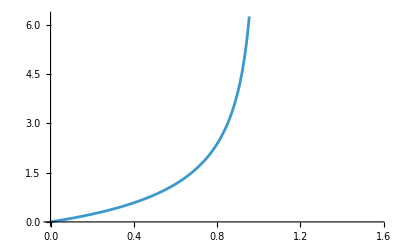

```mathematica
Plot[Derivative[1,1,0,0][Hypergeometric2F1][0,1,1,x],{x,0,π/2}]
```

```mathematica
HypergeomSimplify[ Derivative[1,1,0,0][Hypergeometric2F1][0,1,1,Ri^2/B^2]]
```

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

1+TerminatedEvaluation[RecursionLimit]

```mathematica
Derivative[2,0,0,0][Hypergeometric2F1][0,1,1,Ri^2/B^2]//N
```

Hypergeometric2F1^(2,0,0,0)[0.,1.,1.,Ri^2/B^2]

```mathematica
-2 Derivative[1,1,0,0][Hypergeometric2F1][0,1,1,Ri^2/B^2]++Derivative[0,2,0,0][Hypergeometric2F1][0,1,1,Ri^2/B^2]/.{B->2,Ri->1}//N
```

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

0.

```mathematica
D[(1-z)^-a,{a,n}]
```

```mathematica
(-1)^n (1-z)^-a Log[1-z]^n/.n->2
```

(1-z)^-a Log[1-z]^2

```mathematica
D[Hypergeometric2F1[a,1,1,z],{a,2}]
```

(1-z)^-a Log[1-z]^2

```mathematica
Log[B]^3+3 Log[B]^2 Log[Cos[θ]]+3 Log[B] Log[Cos[θ]]^2+Log[Cos[θ]]^3/.BθToRs//FullSimplify
```

-1/8 (Log[1+(4 Ri^2)/(3 si^2)]-Log[Ri^2+(3 si^2)/4])^3

```mathematica
Table[T[n+i,si,Ri,θsi,ϕsi,θRi,ϕRi]/.{Ψ111->psi111,Y[l_,m_,θsi,ϕsi]->Exp[m I l θsi],Y[l_,m_,θRi,ϕRi]->Exp[m I l θRi]},{i,1,0-n}]/.{n->-2}
```

Table::iterb: Iterator {i,1,-n} does not have appropriate bounds.

{Null,1/8 Log[B^2-Ri^2]^2}

```mathematica
T[-2,si,Ri,θsi,ϕsi,θRi,ϕRi]
```

0

(π r_0 Y[0,0,θRi,ϕRi] Y[0,0,θsi,ϕsi])/(8 Ri^2)+(si^2 (1/16 a_2 r_2 Y[2,-1,θsi,ϕsi] Y[2,1,θRi,ϕRi]+1/16 a_2 r_2 Y[2,-1,θRi,ϕRi] Y[2,1,θsi,ϕsi]))/Ri^4

处理的Ylm对：{{0,0,0,0},{2,-1,2,1},{2,1,2,-1}}

nextTerm:3/Ri^2

ExpansionLwave(π r_0 Y[0,0,θRi,ϕRi] Y[0,0,θsi,ϕsi])/(8 Ri^2)

nextTerm:4/(3 si^2)

ExpansionLwave(si^2 a_2 r_2 Y[2,-1,θsi,ϕsi] Y[2,1,θRi,ϕRi])/(16 Ri^4)

$Aborted

```mathematica
FreeQ[1/8 Log[B^2-Ri^2]^2,Ri]
```

False

```mathematica
TnextExpand[1/8 Log[B^2-Ri^2]^2,-2]
```

0

```mathematica
NextSmallTExpansion[1/8 Log[B^2-Ri^2]^2]/.TwoBodyF[_,_,_,_]->0
```

(1/4 Log[4/3]^2+(3 Log[Ri]^2)/2+Log[Ri] Log[(3 √3 si)/(8 Ri)]+1/2 Log[(√3 si)/(2 Ri)]^2) Log[si/a_0] Y[0,0,θRi,ϕRi] Y[0,0,θsi,ϕsi]-((si^2/4-1/4 si^2 Log[si/a_0]-(π r_0)/4) Y[0,0,θRi,ϕRi] Y[0,0,θsi,ϕsi])/(2 Ri^2)+((6 Ri^2 (1+Log[4/3])-12 Ri^2 Log[Ri]) (si^2/8-(4 a_2)/(π si^2)) Y[2,-1,θsi,ϕsi] Y[2,1,θRi,ϕRi])/(12 Ri^4)-((-si^4/96-a_2/π-1/16 si^2 a_2 r_2) Y[2,-1,θsi,ϕsi] Y[2,1,θRi,ϕRi])/Ri^4+((6 Ri^2 (1+Log[4/3])-12 Ri^2 Log[Ri]) (si^2/8-(4 a_2)/(π si^2)) Y[2,-1,θRi,ϕRi] Y[2,1,θsi,ϕsi])/(12 Ri^4)-((-si^4/96-a_2/π-1/16 si^2 a_2 r_2) Y[2,-1,θRi,ϕRi] Y[2,1,θsi,ϕsi])/Ri^4+((11+Log[4096/729]-12 Log[Ri]) (si^4/384-(96 a_4)/(π si^4)) Y[4,-1,θsi,ϕsi] Y[4,1,θRi,ϕRi])/(2 Ri^4)+((11+Log[4096/729]-12 Log[Ri]) (si^4/384-(96 a_4)/(π si^4)) Y[4,-1,θRi,ϕRi] Y[4,1,θsi,ϕsi])/(2 Ri^4)

```mathematica
Psi111ToSmallt[1/8 Log[B^2-Ri^2]^2]
```

```mathematica
CompareCoefficient[{1/8 Log[B^2-Ri^2]^2},-1]
```

0

```mathematica
Clear[T]
```

```mathematica
T[-2,si,Ri,θsi,ϕsi,θRi,ϕRi]
```

0

0

```mathematica
N[1/2 (-Derivative[0,1,0,0][Hypergeometric2F1][0,1,1,Ri^2/B^2]+Derivative[1,0,0,0][Hypergeometric2F1][0,1,1,Ri^2/B^2])/.{Ri->1,B->2},20]
```

0.14384103622589046372

```mathematica
psi111[-3,0,-1,0,1,B,θ,θsi,ϕsi,θRi,ϕRi,0]
```

(4 EllipticE[Ri^2/B^2]-2 EllipticK[Ri^2/B^2])/(B^3 π)

```mathematica
Psi111ToSmallt[psi111[-5,0,-1,0,1,B,θ,θsi,ϕsi,θRi,ϕRi,2]]
```

$Aborted

```mathematica
HypergeomSimplify[Derivative[0,1,0,0][Hypergeometric2F1][0,1,1,0.1]-Derivative[1,0,0,0][Hypergeometric2F1][0,1,1,0.1]]
```

-0.105361

```mathematica
(psi111[0,0,-1,0,1,B,θ,θsi,ϕsi,θRi,ϕRi,2]-psi1111[0,0,-1,0,1,B,θ,θsi,ϕsi,θRi,ϕRi,2])/.{Ri->1,B->2}//N
```

0.0772583

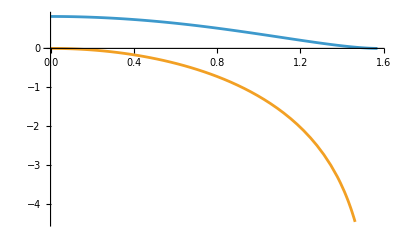

```mathematica
Plot[{π^2/12-PolyLog[2,Sin[θ]^2]/2,Log[Cos[θ]^2]},{θ,0,π/2}]
```

```mathematica
1/48 Log[B^2-Ri^2]^3/.{Ri->B Sin[θ]}//FullSimplify
```

```mathematica
1/8(2Log[B ]+2Log[Cos[θ]])^3//Expand
```

Log[B]^3+3 Log[B]^2 Log[Cos[θ]]+3 Log[B] Log[Cos[θ]]^2+Log[Cos[θ]]^3

```mathematica
psi111[0,0,-1,0,1,B,θ,θsi,ϕsi,θRi,ϕRi,2]/.{Ri->B Sin[θ]}//FullSimplify
```

```mathematica
1/4 (2Log[B]+2Log[ Cos[θ]])^2//Expand
```

Log[B]^2+2 Log[B] Log[Cos[θ]]+Log[Cos[θ]]^2

```mathematica
Log[B]+1/2 Log[Cos[θ]^2]
```

```mathematica
Log[1-Ri^2/B^2]/.{Ri->B Sin[θ]}//FullSimplify
```

Log[Cos[θ]^2]

```mathematica
Length@Flatten[Cases[reduceYTable[psi111[-6,3,-1,3,1,B,θ,θsi,ϕsi,θRi,ϕRi,0]],{1,-1,1,1,__}]]
```

0

```mathematica
reduceYTable[psi111[-4,1,-1,1,1,B,θ,θsi,ϕsi,θRi,ϕRi,0]]
```

{{1,-1,1,1,(3 √3 si)/(4 Ri^5)-(27 √3 si^3)/(16 Ri^7)+(81 √3 si^5)/(32 Ri^9)-(405 √3 si^7)/(128 Ri^11)},{1,1,1,-1,-(3 √3 si)/(4 Ri^5)+(27 √3 si^3)/(16 Ri^7)-(81 √3 si^5)/(32 Ri^9)+(405 √3 si^7)/(128 Ri^11)}}

```mathematica
psi1111[-6,3,-1,3,1,B,θ,θsi,ϕsi,θRi,ϕRi,1]
```

-3 ⅇ^(3 ⅈ θRi-3 ⅈ θsi) Sin[2 ArcTan[(2 Ri)/(√3 si)]]^3 (-(8 B^2 (10 B^4-15 B^2 Ri^2+6 Ri^4) (1/(768 B^6)+1/2 (1/(768 B^6)+1/4 (1/(288 B^6)+1/6 (1/(64 B^6)+Log[B]/(8 B^6))))))/(5 (B^2-Ri^2)^3)+1/(384 B^6)((B^2 (10-(10 B^2)/Ri^2) (5 B^8-10 B^6 Ri^2+10 B^4 Ri^4-5 B^2 Ri^6+Ri^8))/(5 (B^2-Ri^2)^5)+4 (-1+B^4/Ri^4) (Hypergeometric2F1^(0,1,0,0)[6,1,1,Ri^2/B^2]-Hypergeometric2F1^(1,0,0,0)[6,1,1,Ri^2/B^2])+1/2 (-48-(8 B^4)/Ri^4-(24 B^2)/Ri^2) (Hypergeometric2F1^(0,1,0,0)[6,1,2,Ri^2/B^2]-Hypergeometric2F1^(1,0,0,0)[6,1,2,Ri^2/B^2])))

```mathematica
Clear[Θ]
```

```mathematica
Θ[3,3,-4,θ]
```

(2 Ri^3 (3+Cos[2 ArcTan[(2 Ri)/(√3 si)]]))/(3 √3 si^3)

```mathematica
Psi111ToSmallt[T[-2,si,Ri,θsi,ϕsi,θRi,ϕRi]/.{Ψ111->psi111}]
```

-(48 ⅈ ⅇ^(ⅈ θRi-ⅈ θsi) a_1^2)/(π^2 Ri si)+(48 ⅈ ⅇ^(-ⅈ θRi+ⅈ θsi) a_1^2)/(π^2 Ri si)-(60 ⅈ ⅇ^(ⅈ θRi-ⅈ θsi) si a_1^2)/(π^2 Ri^3)+(60 ⅈ ⅇ^(-ⅈ θRi+ⅈ θsi) si a_1^2)/(π^2 Ri^3)+(45 ⅈ ⅇ^(ⅈ θRi-ⅈ θsi) si^3 a_1^2)/(π^2 Ri^5)-(45 ⅈ ⅇ^(-ⅈ θRi+ⅈ θsi) si^3 a_1^2)/(π^2 Ri^5)-(24 ⅈ ⅇ^(3 ⅈ θRi-3 ⅈ θsi) si^3 a_1^2)/(π^2 Ri^5)+(24 ⅈ ⅇ^(-3 ⅈ θRi+3 ⅈ θsi) si^3 a_1^2)/(π^2 Ri^5)-(135 ⅈ ⅇ^(ⅈ θRi-ⅈ θsi) si^5 a_1^2)/(4 π^2 Ri^7)+(135 ⅈ ⅇ^(-ⅈ θRi+ⅈ θsi) si^5 a_1^2)/(4 π^2 Ri^7)+(18 ⅈ ⅇ^(3 ⅈ θRi-3 ⅈ θsi) si^5 a_1^2)/(π^2 Ri^7)-(18 ⅈ ⅇ^(-3 ⅈ θRi+3 ⅈ θsi) si^5 a_1^2)/(π^2 Ri^7)-(6 ⅈ ⅇ^(5 ⅈ θRi-5 ⅈ θsi) si^5 a_1^2)/(π^2 Ri^7)+(6 ⅈ ⅇ^(-5 ⅈ θRi+5 ⅈ θsi) si^5 a_1^2)/(π^2 Ri^7)

0

```mathematica
Exponent[T[-2,si,Ri,θsi,ϕsi,θRi,ϕRi]/.{Ψ111->psi111}/.BθToRs/.{si->2/(√3)t Ri},Ri]
```

2

```mathematica
T[-10,si,Ri,θsi,ϕsi,θRi,ϕRi]
```

0

(Ri ((6 ⅈ a_1 Y[1,-1,θsi,ϕsi] Y[1,1,θRi,ϕRi])/π-(6 ⅈ a_1 Y[1,-1,θRi,ϕRi] Y[1,1,θsi,ϕsi])/π))/si

处理的Ylm对：{{1,-1,1,1},{1,1,1,-1}}

nextTerm:(2 Ri)/(√3 si)

ExpansionLwave(6 ⅈ Ri a_1 Y[1,-1,θsi,ϕsi] Y[1,1,θRi,ϕRi])/(π si)

nextTerm:(2 Ri)/(√3 si)

ExpansionLwave-(6 ⅈ Ri a_1 Y[1,-1,θRi,ϕRi] Y[1,1,θsi,ϕsi])/(π si)

结果为(3 ⅈ √3 a_1 Ψ111[0,1,-1,1,1,B,θ,θsi,ϕsi,θRi,ϕRi,0])/π-(3 ⅈ √3 a_1 Ψ111[0,1,1,1,-1,B,θ,θsi,ϕsi,θRi,ϕRi,0])/π

0

(-(48 ⅈ a_1^2 Y[1,-1,θsi,ϕsi] Y[1,1,θRi,ϕRi])/π^2+(48 ⅈ a_1^2 Y[1,-1,θRi,ϕRi] Y[1,1,θsi,ϕsi])/π^2)/(Ri si)

处理的Ylm对：{{1,-1,1,1},{1,1,1,-1}}

nextTerm:2/(√3 Ri si)

ExpansionLwave-(48 ⅈ a_1^2 Y[1,-1,θsi,ϕsi] Y[1,1,θRi,ϕRi])/(π^2 Ri si)

nextTerm:2/(√3 Ri si)

ExpansionLwave(48 ⅈ a_1^2 Y[1,-1,θRi,ϕRi] Y[1,1,θsi,ϕsi])/(π^2 Ri si)

结果为-(24 ⅈ √3 a_1^2 Ψ111[-2,1,-1,1,1,B,θ,θsi,ϕsi,θRi,ϕRi,0])/π^2+(24 ⅈ √3 a_1^2 Ψ111[-2,1,1,1,-1,B,θ,θsi,ϕsi,θRi,ϕRi,0])/π^2

0

((240 ⅈ a_1^3 Y[1,-1,θsi,ϕsi] Y[1,1,θRi,ϕRi])/π^3-(240 ⅈ a_1^3 Y[1,-1,θRi,ϕRi] Y[1,1,θsi,ϕsi])/π^3)/(Ri^3 si)+(si (-(720 ⅈ Log[si/Rc_1] a_1^3 Y[1,-1,θsi,ϕsi] Y[1,1,θRi,ϕRi])/π^3+(720 ⅈ Log[si/Rc_1] a_1^3 Y[1,-1,θRi,ϕRi] Y[1,1,θsi,ϕsi])/π^3))/Ri^5+(si^3 ((144 ⅈ a_1^2 a_3 r_3 Y[3,-1,θsi,ϕsi] Y[3,1,θRi,ϕRi])/π^2-(144 ⅈ a_1^2 a_3 r_3 Y[3,-1,θRi,ϕRi] Y[3,1,θsi,ϕsi])/π^2))/Ri^7+(si^5 ((54 ⅈ a_1^2 a_5 r_5 Y[5,-1,θsi,ϕsi] Y[5,1,θRi,ϕRi])/π^2-(54 ⅈ a_1^2 a_5 r_5 Y[5,-1,θRi,ϕRi] Y[5,1,θsi,ϕsi])/π^2))/Ri^9+(si^7 ((18 ⅈ a_1^2 a_7 r_7 Y[7,-1,θsi,ϕsi] Y[7,1,θRi,ϕRi])/π^2-(18 ⅈ a_1^2 a_7 r_7 Y[7,-1,θRi,ϕRi] Y[7,1,θsi,ϕsi])/π^2))/Ri^11

处理的Ylm对：{{1,-1,1,1},{1,1,1,-1},{3,-1,3,1},{3,1,3,-1},{5,-1,5,1},{5,1,5,-1},{7,-1,7,1},{7,1,7,-1}}

nextTerm:(3 √3 si)/(4 Ri^5)

ExpansionLwave((240 ⅈ a_1^3)/(π^3 Ri^3 si)-(720 ⅈ si Log[si/Rc_1] a_1^3)/(π^3 Ri^5)) Y[1,-1,θsi,ϕsi] Y[1,1,θRi,ϕRi]

nextTerm:1/(2 √3 Ri^3 si)

ExpansionLwave((240 ⅈ a_1^3)/(π^3 Ri^3 si)-(720 ⅈ si Log[si/Rc_1] a_1^3)/(π^3 Ri^5)) Y[1,-1,θsi,ϕsi] Y[1,1,θRi,ϕRi]

nextTerm:(3 √3 si)/(4 Ri^5)

ExpansionLwave(-(240 ⅈ a_1^3)/(π^3 Ri^3 si)+(720 ⅈ si Log[si/Rc_1] a_1^3)/(π^3 Ri^5)) Y[1,-1,θRi,ϕRi] Y[1,1,θsi,ϕsi]

nextTerm:1/(2 √3 Ri^3 si)

ExpansionLwave(-(240 ⅈ a_1^3)/(π^3 Ri^3 si)+(720 ⅈ si Log[si/Rc_1] a_1^3)/(π^3 Ri^5)) Y[1,-1,θRi,ϕRi] Y[1,1,θsi,ϕsi]

nextTerm:4/(3 √3 Ri si^3)

ExpansionLwave(144 ⅈ si^3 a_1^2 a_3 r_3 Y[3,-1,θsi,ϕsi] Y[3,1,θRi,ϕRi])/(π^2 Ri^7)

$Aborted

```mathematica
FullSimplify[(1680 ⅈ Subscript[a, 1]^4)/(π^4 Ri^5 si)+(4320 ⅈ Log[3] Subscript[a, 1]^4)/(π^4 Ri^5 si)-(8640 ⅈ Log[2 Ri] Subscript[a, 1]^4)/(π^4 Ri^5 si)+(2880 ⅈ Log[si/Ri] Subscript[a, 1]^4)/(π^4 Ri^5 si)]
```

(240 ⅈ (7+18 Log[3]-36 Log[2 Ri]+12 Log[si/Ri]) a_1^4)/(π^4 Ri^5 si)

```mathematica
nMax
```

5

```mathematica
Psi111ToSmallt[Ψ111[-6,1,-1,1,1,B,θ,θsi,ϕsi,θRi,ϕRi,1]/.Ψ111->psi111]
```

0

```mathematica
DB[0] Ψ111[-4,1,-1,1,1,B,θ,θsi,ϕsi,θRi,ϕRi,0]+DB[0] Ψ111[-4,1,1,1,-1,B,θ,θsi,ϕsi,θRi,ϕRi,0]/.Ψ111->psi111//FullSimplify
```

(√3 Ri si Cos[θRi-θsi] DB[0])/B^6

```mathematica
N[Derivative[0,1,0,0][Hypergeometric2F1][0,3,2,Ri^2/B^2]-Derivative[1,0,0,0][Hypergeometric2F1][0,3,2,Ri^2/B^2]/.{Ri->1,B->5},20]
```

-0.061655327853588462888

```mathematica
Clear[EnhancedHypergeomSimplify]
```

```mathematica
EnhancedHypergeomSimplify[Derivative[0,1,0,0][Hypergeometric2F1][0,3,2,Ri^2/B^2]-Derivative[1,0,0,0][Hypergeometric2F1][0,3,2,Ri^2/B^2]]
```

0

```mathematica
(Ψ111[2,1,-1,1,1,B,θ,θsi,ϕsi,θRi,ϕRi,1]/.Ψ111->psi1111)
```

1/4 √3 ⅇ^(ⅈ θRi-ⅈ θsi) Ri si (2 Log[B]+Hypergeometric2F1^(0,1,0,0)[0,3,2,Ri^2/B^2]-Hypergeometric2F1^(1,0,0,0)[0,3,2,Ri^2/B^2])

```mathematica
Ψ111[2,1,-1,1,1,B,θ,θsi,ϕsi,θRi,ϕRi,1]/.Ψ111->psi111
```

1/2 √3 ⅇ^(ⅈ (θRi-θsi)) Ri si Log[B]

```mathematica
Re@((Ψ111[0,1,-1,1,1,B,θ,0,ϕsi,0,ϕRi,1]/.Ψ111->psi1111)-Ψ111[0,1,-1,1,1,B,θ,0,ϕsi,0,ϕRi,1]/.Ψ111->psi111)/.{B->5}
```

Re[-(√3 Ri si Log[(5-Ri) (5+Ri)])/(100-4 Ri^2)+1/2 √3 Ri si (Log[5]/(25 (1-Ri^2/25))+1/50 (Hypergeometric2F1^(0,1,0,0)[1,2,2,Ri^2/25]-Hypergeometric2F1^(1,0,0,0)[1,2,2,Ri^2/25]))]

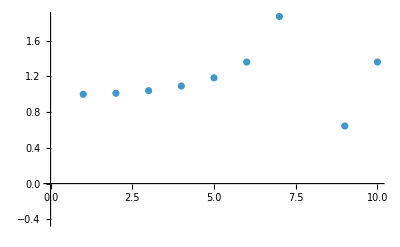

```mathematica
ListPlot[Table[Re@((Ψ111[-6,1,-1,1,1,B,θ,0,ϕsi,0,ϕRi,1]/.Ψ111->psi1111)/Ψ111[-6,1,-1,1,1,B,θ,0,ϕsi,0,ϕRi,1]/.Ψ111->psi111)/.{B->5,si->1},{Ri,0.1,5,0.5}]//N]
```

```mathematica
Ψ111[0,1,-1,1,1,B,θ,θsi,ϕsi,θRi,ϕRi,1]/.Ψ111->psi111/.{Ri->1,B->5}//N
```

0.0573391 2.71828^((0.+1. ⅈ) (θRi-1. θsi)) si

```mathematica
Psi111ToSmallt[Ψ111[-6,1,-1,1,1,B,θ,θsi,ϕsi,θRi,ϕRi,4]/.Ψ111->psi111]
```

0

```mathematica
(+1/π^3 480 ⅈ √3 Subscript[a, 1]^3 Ψ111[-4,1,-1,1,1,B,θ,θsi,ϕsi,θRi,ϕRi,1]-1/π^3 480 ⅈ √3 Subscript[a, 1]^3 Ψ111[-4,1,1,1,-1,B,θ,θsi,ϕsi,θRi,ϕRi,1])/B0[n,0,0,0,0,si,Ri,θsi,ϕsi,θRi,ϕRi]/.Ψ111->psi111//FullSimplify
```

```mathematica
-((360 (Ri^2+2 (B-Ri) (B+Ri) (2 Log[B]-Log[1-Ri^2/B^2])) Subscript[a, 1]^3)/( π^3 (B-Ri) (B+Ri)))/.BθToRs//FullSimplify
```

```mathematica
FullSimplify[LogContract[-(240 (2 Ri^2+3 si^2 (Log[B^2]-Log[(3 si^2)/(4 B^2)])) Subscript[a, 1]^3)/(π^3 si^2 B^6),Assumptions->Automatic],Assumptions->{si>0,B>0}]
```

-(240 (2 Ri^2+si^2 Log[64/27]+3 si^2 Log[B^4/si^2]) a_1^3)/(B^6 π^3 si^2)

```mathematica
T[-6,si,Ri,θsi,ϕsi,θRi,ϕRi]
```

0

1/(Ri^5 si)((1680 ⅈ a_1^4 Y[1,-1,θsi,ϕsi] Y[1,1,θRi,ϕRi])/π^4+(4320 ⅈ Log[3] a_1^4 Y[1,-1,θsi,ϕsi] Y[1,1,θRi,ϕRi])/π^4-(8640 ⅈ Log[2 Ri] a_1^4 Y[1,-1,θsi,ϕsi] Y[1,1,θRi,ϕRi])/π^4+(2880 ⅈ Log[si/Ri] a_1^4 Y[1,-1,θsi,ϕsi] Y[1,1,θRi,ϕRi])/π^4-(1680 ⅈ a_1^4 Y[1,-1,θRi,ϕRi] Y[1,1,θsi,ϕsi])/π^4-(4320 ⅈ Log[3] a_1^4 Y[1,-1,θRi,ϕRi] Y[1,1,θsi,ϕsi])/π^4+(8640 ⅈ Log[2 Ri] a_1^4 Y[1,-1,θRi,ϕRi] Y[1,1,θsi,ϕsi])/π^4-(2880 ⅈ Log[si/Ri] a_1^4 Y[1,-1,θRi,ϕRi] Y[1,1,θsi,ϕsi])/π^4)+1/(Ri^3 si^3)(-(2304 ⅈ a_1 a_3 Y[3,-1,θsi,ϕsi] Y[3,1,θRi,ϕRi])/π^2+(2304 ⅈ a_1 a_3 Y[3,-1,θRi,ϕRi] Y[3,1,θsi,ϕsi])/π^2)

处理的Ylm对：{{1,-1,1,1},{1,1,1,-1},{3,-1,3,1},{3,1,3,-1}}

Part::partw: Part 5 of {} does not exist.

{}⟦5⟧

((1680 ⅈ a_1^4)/(π^4 Ri^5 si)+(4320 ⅈ Log[3] a_1^4)/(π^4 Ri^5 si)-(8640 ⅈ Log[2 Ri] a_1^4)/(π^4 Ri^5 si)+(2880 ⅈ Log[si/Ri] a_1^4)/(π^4 Ri^5 si)) Y[1,-1,θsi,ϕsi] Y[1,1,θRi,ϕRi]

Part::partw: Part 5 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{}⟦5⟧

((1680 ⅈ a_1^4)/(π^4 Ri^5 si)+(4320 ⅈ Log[3] a_1^4)/(π^4 Ri^5 si)-(8640 ⅈ Log[2 Ri] a_1^4)/(π^4 Ri^5 si)+(2880 ⅈ Log[si/Ri] a_1^4)/(π^4 Ri^5 si)) Y[1,-1,θsi,ϕsi] Y[1,1,θRi,ϕRi]

$Aborted

```mathematica
Collect[Plus@@DeleteCases[Table[T[-3+i,si,Ri,θsi,ϕsi,θRi,ϕRi]/T[2,si,Ri,θsi,ϕsi,θRi,ϕRi],{i,0,5}],Null]/.{Ψ111->psi111},B]//Expand
```

```mathematica
1-(9 ⅈ ⅇ^(ⅈ θRi-ⅈ θsi) Ri si Subscript[a, 1])/(2 π (-B^2+Ri^2) (Ri si Cos[θsi] Sin[θRi]-Ri si Cos[θRi] Sin[θsi]))+(9 ⅈ ⅇ^(-ⅈ θRi+ⅈ θsi) Ri si Subscript[a, 1])/(2 π (-B^2+Ri^2) (Ri si Cos[θsi] Sin[θRi]-Ri si Cos[θRi] Sin[θsi]))-(36 ⅈ ⅇ^(ⅈ θRi-ⅈ θsi) Ri si Subscript[a, 1]^2)/(B^2 π^2 (B^2-Ri^2) (Ri si Cos[θsi] Sin[θRi]-Ri si Cos[θRi] Sin[θsi]))+(36 ⅈ ⅇ^(-ⅈ θRi+ⅈ θsi) Ri si Subscript[a, 1]^2)/(B^2 π^2 (B^2-Ri^2) (Ri si Cos[θsi] Sin[θRi]-Ri si Cos[θRi] Sin[θsi]))//FullSimplify
```

```mathematica
1-(9 (B^2 π-8 Subscript[a, 1]) Subscript[a, 1])/(B^2 π^2 (B^2-Ri^2))/.Ri->B Sin[θ]//Simplify//Expand
```

1-(9 Sec[θ]^2 a_1)/(B^2 π)+(72 Sec[θ]^2 a_1^2)/(B^4 π^2)

```mathematica
Ri si Sin[θRi-θsi]-(9 ⅈ ⅇ^(ⅈ θRi-ⅈ θsi) Ri si Subscript[a, 1])/(2 π (-B^2+Ri^2))+(9 ⅈ ⅇ^(-ⅈ θRi+ⅈ θsi) Ri si Subscript[a, 1])/(2 π (-B^2+Ri^2))-(36 ⅈ ⅇ^(ⅈ θRi-ⅈ θsi) Ri si Subscript[a, 1]^2)/(B^2 π^2 (B^2-Ri^2))+(36 ⅈ ⅇ^(-ⅈ θRi+ⅈ θsi) Ri si Subscript[a, 1]^2)/(B^2 π^2 (B^2-Ri^2))
```

```mathematica
1-(9 (B^2 π-8 Subscript[a, 1]) Subscript[a, 1])/(B^2 π^2 (B^2-Ri^2))/.{Ri->B Sin[θ]}//FullSimplify
```

1-(9 Sec[θ]^2 (B^2 π-8 a_1) a_1)/(B^4 π^2)

(Ri si Sin[θRi-θsi] (B^2 π^2 (B-Ri) (B+Ri)-9 B^2 π a_1+72 a_1^2))/(B^2 π^2 (B-Ri) (B+Ri))

```mathematica
ⅈ/(√3)(psi111[0,1,1,1,-1,B,θ,θsi,ϕsi,θRi,ϕRi]-psi111[0,1,-1,1,1,B,θ,θsi,ϕsi,θRi,ϕRi])//FullSimplify
```

(Ri si Sin[θRi-θsi])/(B^2-Ri^2)

```mathematica
psi111[4,1,1,1,1,B,θ,θsi,ϕsi,θRi,ϕRi,0]
```

1/2 √3 ⅇ^(ⅈ θRi+ⅈ θsi) Ri (B^2-2 Ri^2) si

```mathematica
(-Ri^2+(3 si^2)/4)/B^6
```

```mathematica
B^2-2 Ri^2/.BθToRs
```

-Ri^2+(3 si^2)/4

```mathematica
(Ri^2 si Ri)/(B^6 si^2)
```

Ri^3/(B^6 si)

```mathematica
psi1112[-4,1,1,1,-1,B,θ,θsi,ϕsi,θRi,ϕRi,0]
```

ComplexInfinity

```mathematica
psi111[-4,1,1,1,1,B,θ,θsi,ϕsi,θRi,ϕRi,0]
```

(√3 ⅇ^(ⅈ θRi+ⅈ θsi) Ri si)/(2 B^6)

```mathematica
ggg=(Coefficient[Collect[tot, Y[_,_,θRi,ϕRi] Y[_,_,θsi,ϕsi]],Y[1,-1,θsi,ϕsi] Y[1,1,θRi,ϕRi]](Y[1,-1,θsi,ϕsi] Y[1,1,θRi,ϕRi]))
```

((80 ⅈ a_1^3)/(27 π^3 Ri^3 si)-(80 ⅈ si Log[si/Rc_1] a_1^3)/(9 π^3 Ri^5)) Y[1,-1,θsi,ϕsi] Y[1,1,θRi,ϕRi]

```mathematica
Exponent[ggg,Ri,Max]
```

-3

```mathematica
(80 ⅈ si Log[si/Subscript[Rc, 1]] Subscript[a, 1]^3)/(9 π^3 Ri^5)
```

```mathematica
getHighestPowerTerm[Flatten[Cases[reduceYTable[psi111[-4,1,-1,1,1,B,θ,θsi,ϕsi,θRi,ϕRi]],{1,-1,1,1,__}]][[5]],Ri]
```

(3 √3 si)/(4 Ri^5)

```mathematica
Coefficient[ggg,Ri,-3]*Ri^-3/(Y[1,1,θRi,ϕRi]*Y[1,-1,θsi,ϕsi])
```

(80 ⅈ a_1^3)/(27 π^3 Ri^3 si)

```mathematica
3/4 √3 ⅇ^(ⅈ θRi-ⅈ θsi) si Log[Ri]-3/4 √3 ⅇ^(-ⅈ θRi+ⅈ θsi) si Log[Ri]//FullSimplify
```

3/2 ⅈ √3 si Log[Ri] Sin[θRi-θsi]

```mathematica
+1/4 √3 ⅇ^(ⅈ θRi-ⅈ θsi) si Derivative[0,1,0,0][Hypergeometric2F1][3,0,2,0]+1/8 √3 ⅇ^(ⅈ θRi-ⅈ θsi) si Derivative[0,1,0,0][Hypergeometric2F1][3,0,2,3/4]-3/8 √3 ⅇ^(-ⅈ θRi+ⅈ θsi) si Derivative[0,1,0,0][Hypergeometric2F1][3,0,2,3/4]+3/32 √3 ⅇ^(ⅈ θRi-ⅈ θsi) si Derivative[0,1,0,1][Hypergeometric2F1][3,0,2,3/4]+3/32 √3 ⅇ^(-ⅈ θRi+ⅈ θsi) si Derivative[0,1,0,1][Hypergeometric2F1][3,0,2,3/4]-1/4 √3 ⅇ^(ⅈ θRi-ⅈ θsi) si Derivative[1,0,0,0][Hypergeometric2F1][3,0,2,0]-1/8 √3 ⅇ^(ⅈ θRi-ⅈ θsi) si Derivative[1,0,0,0][Hypergeometric2F1][3,0,2,3/4]+3/8 √3 ⅇ^(-ⅈ θRi+ⅈ θsi) si Derivative[1,0,0,0][Hypergeometric2F1][3,0,2,3/4]-3/32 √3 ⅇ^(ⅈ θRi-ⅈ θsi) si Derivative[1,0,0,1][Hypergeometric2F1][3,0,2,3/4]-3/32 √3 ⅇ^(-ⅈ θRi+ⅈ θsi) si Derivative[1,0,0,1][Hypergeometric2F1][3,0,2,3/4]
```

si ((0.+2.4996 ⅈ) Sin[1. θRi-1. θsi]+Cos[1. θRi-1. θsi] (2.64731-0.32476 Hypergeometric2F1^(1,0,0,1)[3.,0.,2.,0.75]))

```mathematica
Coefficient[Psi111ToSmallt[psi111[-4,1,-1,1,1,B,θ,θsi,ϕsi,θRi,ϕRi,1]],Ri^-5]
```

3/4 √3 ⅇ^(ⅈ θRi-ⅈ θsi) si Log[Ri]-3/4 √3 ⅇ^(-ⅈ θRi+ⅈ θsi) si Log[Ri]+1/4 √3 ⅇ^(ⅈ θRi-ⅈ θsi) si Hypergeometric2F1^(0,1,0,0)[3,0,2,0]+1/8 √3 ⅇ^(ⅈ θRi-ⅈ θsi) si Hypergeometric2F1^(0,1,0,0)[3,0,2,3/4]-3/8 √3 ⅇ^(-ⅈ θRi+ⅈ θsi) si Hypergeometric2F1^(0,1,0,0)[3,0,2,3/4]+3/32 √3 ⅇ^(ⅈ θRi-ⅈ θsi) si Hypergeometric2F1^(0,1,0,1)[3,0,2,3/4]+3/32 √3 ⅇ^(-ⅈ θRi+ⅈ θsi) si Hypergeometric2F1^(0,1,0,1)[3,0,2,3/4]-1/4 √3 ⅇ^(ⅈ θRi-ⅈ θsi) si Hypergeometric2F1^(1,0,0,0)[3,0,2,0]-1/8 √3 ⅇ^(ⅈ θRi-ⅈ θsi) si Hypergeometric2F1^(1,0,0,0)[3,0,2,3/4]+3/8 √3 ⅇ^(-ⅈ θRi+ⅈ θsi) si Hypergeometric2F1^(1,0,0,0)[3,0,2,3/4]-3/32 √3 ⅇ^(ⅈ θRi-ⅈ θsi) si Hypergeometric2F1^(1,0,0,1)[3,0,2,3/4]-3/32 √3 ⅇ^(-ⅈ θRi+ⅈ θsi) si Hypergeometric2F1^(1,0,0,1)[3,0,2,3/4]

```mathematica
psi111[-4,1,-1,1,1,B,θ,θsi,ϕsi,θRi,ϕRi,3]
```

1/(32 √3 B^6)ⅇ^(ⅈ θRi-ⅈ θsi) Ri si (8 Log[B]^3+12 Log[B]^2 Hypergeometric2F1^(0,1,0,0)[3,0,2,Ri^2/B^2]+6 Log[B] Hypergeometric2F1^(0,2,0,0)[3,0,2,Ri^2/B^2]+Hypergeometric2F1^(0,3,0,0)[3,0,2,Ri^2/B^2]-12 Log[B]^2 Hypergeometric2F1^(1,0,0,0)[3,0,2,Ri^2/B^2]-12 Log[B] Hypergeometric2F1^(1,1,0,0)[3,0,2,Ri^2/B^2]-3 Hypergeometric2F1^(1,2,0,0)[3,0,2,Ri^2/B^2]+6 Log[B] Hypergeometric2F1^(2,0,0,0)[3,0,2,Ri^2/B^2]+3 Hypergeometric2F1^(2,1,0,0)[3,0,2,Ri^2/B^2]-Hypergeometric2F1^(3,0,0,0)[3,0,2,Ri^2/B^2])

```mathematica
psi111[-4,1,-1,1,1,B,θ,θsi,ϕsi,θRi,ϕRi,0]-psi111[-4,1,1,1,-1,B,θ,θsi,ϕsi,θRi,ϕRi,0]//FullSimplify
```

(ⅈ √3 Ri si Sin[θRi-θsi])/B^6

0

(Ri ((6 ⅈ a_1 Y[1,-1,θsi,ϕsi] Y[1,1,θRi,ϕRi])/π-(6 ⅈ a_1 Y[1,-1,θRi,ϕRi] Y[1,1,θsi,ϕsi])/π))/si

处理的Ylm对：{{1,-1,1,1},{1,1,1,-1}}

(9 √3 si)/(2 Ri)

(6 ⅈ Ri a_1 Y[1,-1,θsi,ϕsi] Y[1,1,θRi,ϕRi])/(π si)

Series::ztest1: Unable to decide whether numeric quantity -Hypergeometric2F1^(1,0,0,0)[1,2,2,0] is equal to zero. Assuming it is.

1/(32 Ri)√3 si (144 Log[Ri]+8 Hypergeometric2F1^(0,1,0,0)[1,2,2,0]+4 Hypergeometric2F1^(0,1,0,0)[1,2,2,3/4]+3 Hypergeometric2F1^(0,1,0,1)[1,2,2,3/4]-8 Hypergeometric2F1^(1,0,0,0)[1,2,2,0]-4 Hypergeometric2F1^(1,0,0,0)[1,2,2,3/4]-3 Hypergeometric2F1^(1,0,0,1)[1,2,2,3/4])

(6 ⅈ Ri a_1 Y[1,-1,θsi,ϕsi] Y[1,1,θRi,ϕRi])/(π si)

$Aborted

```mathematica
T[-2,si,Ri,θsi,ϕsi,θRi,ϕRi]+T[0,si,Ri,θsi,ϕsi,θRi,ϕRi]+T[2,si,Ri,θsi,ϕsi,θRi,ϕRi]/.Ψ111->psi111
```

Ri si Cos[θsi] Sin[θRi]-Ri si Cos[θRi] Sin[θsi]-(8 ⅈ ⅇ^(ⅈ θRi-ⅈ θsi) Ri^3 a_1)/(3 π si (-4 B^2+3 si^2))+(8 ⅈ ⅇ^(-ⅈ θRi+ⅈ θsi) Ri^3 a_1)/(3 π si (-4 B^2+3 si^2))-(64 ⅈ ⅇ^(ⅈ θRi-ⅈ θsi) Ri^3 a_1^2)/(27 B^2 π^2 si (4 B^2-3 si^2))+(64 ⅈ ⅇ^(-ⅈ θRi+ⅈ θsi) Ri^3 a_1^2)/(27 B^2 π^2 si (4 B^2-3 si^2))

```mathematica
TnextExpand[Ri si Cos[θsi] Sin[θRi]-Ri si Cos[θRi] Sin[θsi]-(8 ⅈ ⅇ^(ⅈ θRi-ⅈ θsi) Ri^3 Subscript[a, 1])/(3 π si (-4 B^2+3 si^2))+(8 ⅈ ⅇ^(-ⅈ θRi+ⅈ θsi) Ri^3 Subscript[a, 1])/(3 π si (-4 B^2+3 si^2))-(64 ⅈ ⅇ^(ⅈ θRi-ⅈ θsi) Ri^3 Subscript[a, 1]^2)/(27 B^2 π^2 si (4 B^2-3 si^2))+(64 ⅈ ⅇ^(-ⅈ θRi+ⅈ θsi) Ri^3 Subscript[a, 1]^2)/(27 B^2 π^2 si (4 B^2-3 si^2)),-4]//Expand
```

(80 ⅈ a_1^3 Y[1,-1,θsi,ϕsi] Y[1,1,θRi,ϕRi])/(27 π^3 Ri^3 si)-(80 ⅈ si Log[si/Rc_1] a_1^3 Y[1,-1,θsi,ϕsi] Y[1,1,θRi,ϕRi])/(9 π^3 Ri^5)-(80 ⅈ a_1^3 Y[1,-1,θRi,ϕRi] Y[1,1,θsi,ϕsi])/(27 π^3 Ri^3 si)+(80 ⅈ si Log[si/Rc_1] a_1^3 Y[1,-1,θRi,ϕRi] Y[1,1,θsi,ϕsi])/(9 π^3 Ri^5)

```mathematica
Psi111ToSmallt[psi111[-2,1,-1,1,1,B,θ,θsi,ϕsi,θRi,ϕRi,0]]
```

(9 √3 ⅇ^(ⅈ θRi-ⅈ θsi) si)/(2 Ri^3)-(27 √3 ⅇ^(ⅈ θRi-ⅈ θsi) si^3)/(8 Ri^5)+(9 √3 ⅇ^(3 ⅈ θRi-3 ⅈ θsi) si^3)/Ri^5

```mathematica
((320 ⅈ Ri^2 Subscript[a, 1]^3 Ψ111[-4,1,-1,1,1,B,θ,θsi,ϕsi,θRi,ϕRi])/(81 √3 π^3 si^2)-(320 ⅈ Ri^2 Subscript[a, 1]^3 Ψ111[-4,1,1,1,-1,B,θ,θsi,ϕsi,θRi,ϕRi])/(81 √3 π^3 si^2))/T[2,si,Ri,θsi,ϕsi,θRi,ϕRi]/.{Ψ111->psi111}//FullSimplify
```

-(320 Ri^2 a_1^3)/(81 B^6 π^3 si^2)

```mathematica
TnextExpand[T[2,si,Ri,θsi,ϕsi,θRi,ϕRi]+T[0,si,Ri,θsi,ϕsi,θRi,ϕRi]+T[-2,si,Ri,θsi,ϕsi,θRi,ϕRi],-4]
```

TnextExpand[Ri si Cos[θsi] Sin[θRi]-Ri si Cos[θRi] Sin[θsi]-(32 ⅈ Ri^2 a_1^2 Ψ111[-2,1,-1,1,1,B,θ,θsi,ϕsi,θRi,ϕRi])/(27 √3 π^2 si^2)+(32 ⅈ Ri^2 a_1^2 Ψ111[-2,1,1,1,-1,B,θ,θsi,ϕsi,θRi,ϕRi])/(27 √3 π^2 si^2)+(4 ⅈ Ri^2 a_1 Ψ111[0,1,-1,1,1,B,θ,θsi,ϕsi,θRi,ϕRi])/(3 √3 π si^2)-(4 ⅈ Ri^2 a_1 Ψ111[0,1,1,1,-1,B,θ,θsi,ϕsi,θRi,ϕRi])/(3 √3 π si^2)]